# LGD model for the film of HfZrO_2

## Definitions

```mathematica
(* fundamental parameters and lengthscale (nm) *)
```

```mathematica
ϵo = 8.85*10^-12; qe = 1.6*10^-19; kB = 1.38*10^-23; nm=10^-9;
```

```mathematica
{1/(2ϵo)1/(2.02*10^5),1/(2ϵo)1/(1.158*10^4)}
```

{279689.,4.87886×10^6}

### definition for static properties

```mathematica
(*Remove[Z1,Z2,A1,A2,LGDflm,aTp,Tfe,aTa,Tafe,βp,χ,βa,γp,γa,Ast,Pst,Ntrials,ω,Nt,col]*)
```

```mathematica
(* preliminary set of LGD parameters of Subscript[PbZrO, 3] *)
```

```mathematica
(*Options[LGDflm]={τA->1,Ae->0.,Ef->1,h->50,ϵb->7,λ->0.2,ϵd->10,dG1->0.2,dG2->0.2,Z1 -> 2, Z2 -> -2, A1->10^-18, A2->10^-18, aTp->1/(2ϵo)1/(2.02*10^5),Tfe->463.2,aTa->1/(2ϵo)1/(1.158*10^4),Tafe->490,βp->-3.825*10^8,χ->1.775428*10^10,βa->-8.22436*10^9 1/4,γp->3.12591*10^9,γa->1.8242*10^11 1/8,Ast->0.15,Pst->0.15,Ntrials->8,ω->10^-3,Nt->5,col->Red,nst->1};*)
```

```mathematica
Options[LGDflm]={τA->1,Ae->0.,Ef->1,h->50,ϵb->7,λ->0.2,ϵd->10,dG1->0.1,dG2->0.1,Z1 ->2, Z2 ->-2, A1->10^-18, A2->10^-18, aTp->1/(2ϵo)1/(2.02*10^5),Tfe->650,aTa->1/(2ϵo)1/(1.158*10^4),Tafe->690,βp->3.825*10^8,χ->1.775428*10^10,βa->8.22436*10^9 1/4,γp->0,γa->0,Ast->0.15,Pst->0.15,Ntrials->8,ω->10^-3,Nt->5,col->Red,nst->1};
```

```mathematica
LGDflm[slct_,U_,T_,Pe_:1,OptionsPattern[]]:=Block[{FactE=10^9,τA,Ae,Ef,p,a,h,λ,dG1,dG2,Z1,Z2,A1,A2,Βp,Χ,Γp,ϵb,ϵd,exp1,exp2,screen,Eq,Eu,Ee,Ff,stabFf,
b,αp,aTp,Tfe,αa,aTa,Tafe,βp,χ,βa,γp,γa,
Pst,Ast,Pv,Av,Χpp,Χaa,sΧap,sAp,Ap,Ep,E0,Ei,int,ans,sol,i,CurieStar,FminSet,Fmin,OrdPar,FE,AFE,namP,numP,Ntrials,ω,Nt,nst,col,Pdyn,Adyn},
{τA,Ae,Ef,h,λ,ϵb,ϵd,dG1,dG2,Z1,Z2,A1,A2,aTp,Tfe,aTa,Tafe,Βp,Χ,βa,Γp,γa,Ast,Pst,Ntrials,ω,Nt,nst,col}=OptionValue[
{τA,Ae,Ef,h,λ,ϵb,ϵd,dG1,dG2,Z1,Z2,A1,A2,aTp,Tfe,aTa,Tafe,βp,χ,βa,γp,γa,Ast,Pst,Ntrials,ω,Nt,nst,col}];
If[Pe≠0,exp1=1/(√Pe)Exp[(qe dG1)/(kB T)];exp2=√Pe Exp[(qe dG2)/(kB T)];
screen=(1+(λ h*nm)/(ϵo(ϵd h+λ ϵb))((qe Z1)^2/(A1 kB T(1+exp1)^2)+(qe Z2)^2/(A2 kB T(1+exp2)^2)));Eq=(λ/(ϵo (h ϵd+λ ϵb))((qe Z1)/(A1 (exp1+1))+(qe Z2)/(A2 (exp2+1))))Ef;Eu=(- (ϵd U)/((h ϵd+λ ϵb)nm))Ef,
screen=1;Eq=0;Eu=- (ϵd U)/((h ϵd+λ ϵb)nm)Ef];Ee=Eq+Eu;αp=(1/2)(λ/(ϵo(ϵd h+λ ϵb)))+screen aTp(T-Tfe);αa=aTa(T-Tafe);{βp ,χ,γp}=screen{Βp,Χ,Γp};Ff[P_,A_]:=
(1/(aTa*Tafe))(αp P^2+βp P^4+χ A^2 P^2+γp P^6-P*Ee+αa A^2+ βa A^4+γa A^6);
Χpp[P_,A_]:=2 αp+12 P^2 βp+30 P^4 γp+2 A^2 χ;(* sA is for A^2 *)
Χaa[P_,A_]:=2 αa+12 A^2 βa+30 A^4 γa+2 P^2 χ;sΧap[P_,A_]:=16 A^2 P^2 χ^2;sAp[P_,sgn_:1]:=Chop[(-(αa+χ P^2))/(βa+If[sgn>0,+1,-1] √(βa^2-3 (αa+χ P^2) γa)),10^-2];
Ap[P_]:=If[Im[sAp[P]]==0∧Re[sAp[P]]>0,√sAp[P],0(*,√sAp[P]*)] ;
Ep[P_]:=If[(Χpp[P,Ap[P]]>0)&&(Χaa[P,Ap[P]]>0)&&(Χpp[P,Ap[P]]Χaa[P,Ap[P]]>sΧap[P,Ap[P]]),2αp P+2χ Ap[P]^2 P+4 βp P^3+6 γp P^5-Ee] ;
(*Em[P_]:=If[Im[sAp[P,-1]]==0∧Re[sAp[P,-1]]>0,2αp P+2χ sAp[P,-1]P+4 βp P^3+6 γp P^5 ];*)
E0[P_]:=If[(Χpp[P,0]>0)&&(Χaa[P,0]>0),2αp P+4 βp P^3+6 γp P^5 -Ee];Ei[P_]:=2αp P+4 βp P^3+6 γp P^5-Ee;(**)
Which[
slct=="func",Ff[Pst,Ast],
slct=="LGDtst",{αp,αa},
slct=="Ploop",ParametricPlot[{{Ep[P]/FactE,P}(*,{E0[P]/FactE,P},{10^-8 Ei[P],P}*)},{P,-Pst ,Pst},AspectRatio->1,PlotRange->Automatic,PlotStyle->{{Thick,col}(*,{Thick,Darker[col]},{Thick,Green}*)},PlotPoints->100],
slct=="Aloop",ParametricPlot[{{Ep[P]/FactE,Ap[P]}(*,{Ep[P]/FactE,-Ap[P]}*)},{P,- Pst,Pst},AspectRatio->1,PlotRange->Automatic,PlotStyle->{{Thick,(*Dashed,*)col},{Thick,(*Dashed,*)col}}],
True,(*the core of the function*)
int={};Do[sol=NMinimize[{Ff[p,a]},{p,a}, Method->{"RandomSearch","SearchPoints"->2, "RandomSeed"->i}];ans={sol[[1]],Chop[{p,a}/.(sol[[2]]),10^-6.]};AppendTo[int,ans],{i,Ntrials}];CurieStar=DeleteDuplicates[int,Chop[#1-#2,10^-6]=={0,{0,0}}&];
Fmin=Min[CurieStarᵀ[[1]]];FminSet=Select[CurieStar,#[[1]]==Fmin&];
(*post-treatment*)OrdPar=FminSetᵀ[[2]];
FE=Min[OrdParᵀ[[1]]];
AFE=Min[Abs[OrdParᵀ[[2]]]];
(* Main discriminator of the phases *)
Which[
FE==0&&AFE==0,numP=0;namP="PE",
FE≠0&&AFE==0,numP=1;namP="FE",
FE==0&&AFE≠0,numP=2;namP="AFE",
FE≠0&&AFE≠0,numP=3;namP="FI"];
(*Selector of the result to output*)
Which[
slct=="raw",CurieStar,
slct=="NM",FminSet,
slct=="Fmin",Fmin,
slct=="OP",OrdPar,
slct=="FE",FE,
slct=="AFE",AFE,
slct=="phase",namP,
slct=="Nph",numP,
slct=="FEi",{FE,AFE}
(**)
]
]]
```

### definition for dynamic loops

```mathematica
(*Options[Loops]={τA->1,Ae->0.,Ef->1,h->50,ϵb->7,λ->0.2,ϵd->10,dG1->0.2,dG2->0.2,Z1 -> 2, Z2 -> -2, A1->10^-18, A2->10^-18, aTp->1/(2ϵo)1/(2.02*10^5),Tfe->460,aTa->1/(2ϵo)1/(1.158*10^4),Tafe->490,βp->-3.825*10^8,χ->1.775428*10^10,βa->-8.22436*10^9 1/4,γp->3.12591*10^9,γa->1.8242*10^11 1/8,Ast->0.15,Pst->0.15,Ntrials->8,ω->10^-3,Nt->5,col->Red,nst->1};*)
```

```mathematica
Options[Loops]={τA->1,Ae->0.,Ef->1,h->50,ϵb->7,λ->0.2,ϵd->10,dG1->0.1,dG2->0.1,Z1 -> 2, Z2 -> -2, A1->10^-18, A2->10^-18, aTp->1/(2ϵo)1/(2.02*10^5),Tfe->650,aTa->1/(2ϵo)1/(1.158*10^4),Tafe->690,βp->3.825*10^8,χ->1.775428*10^10,βa->8.22436*10^9 1/4,γp->0,γa->0,Ast->0.15,Pst->0.15,Ntrials->8,ω->10^-3,Nt->5,col->Red,nst->1};
```

```mathematica
Loops[slct_,U_,T_,Pe_:1,OptionsPattern[]]:=Block[{FactE=10^9,τA,Ae,Ef,p,a,h,λ,dG1,dG2,Z1,Z2,A1,A2,Βp,Χ,Γp,ϵb,ϵd,exp1,exp2,screen,Eq,Eu,Ee,Ff,stabFf,
b,αp,aTp,Tfe,αa,aTa,Tafe,βp,χ,βa,γp,γa,
Pst,Ast,Pv,Av,Emin,Emax,Pmin,Pmax,Ntrials,ω,Nt,nst,col,Pdyn,Adyn,IposUp,IposDown,InegUp,InegDown},
{τA,Ae,Ef,h,λ,ϵb,ϵd,dG1,dG2,Z1,Z2,A1,A2,aTp,Tfe,aTa,Tafe,Βp,Χ,βa,Γp,γa,Ast,Pst,Ntrials,ω,Nt,nst,col}=OptionValue[
{τA,Ae,Ef,h,λ,ϵb,ϵd,dG1,dG2,Z1,Z2,A1,A2,aTp,Tfe,aTa,Tafe,βp,χ,βa,γp,γa,Ast,Pst,Ntrials,ω,Nt,nst,col}];
If[Pe≠0,exp1=1/(√Pe)Exp[(qe dG1)/(kB T)];exp2=√Pe Exp[(qe dG2)/(kB T)];
screen=(1+(λ h*nm)/(ϵo(ϵd h+λ ϵb))((qe Z1)^2/(A1 kB T(1+exp1)^2)+(qe Z2)^2/(A2 kB T(1+exp2)^2)));Eq=(λ/(ϵo (h ϵd+λ ϵb))((qe Z1)/(A1 (exp1+1))+(qe Z2)/(A2 (exp2+1))))Ef;Eu=(- (ϵd U)/((h ϵd+λ ϵb)nm))Ef,
screen=1;Eq=0;Eu=- (ϵd U)/((h ϵd+λ ϵb)nm)Ef];Ee=Eq+Eu;αp=(1/2)(λ/(ϵo(ϵd h+λ ϵb)))+screen aTp(T-Tfe);αa=aTa(T-Tafe);{βp ,χ,γp}=screen{Βp,Χ,Γp};Ff[P_,A_]:=
(1/(aTa*Tafe))(αp P^2+βp P^4+χ A^2 P^2+γp P^6-P*Ee+αa A^2+ βa A^4+γa A^6);
{Pdyn,Adyn}={Pv,Av}/.First[NDSolve[{
0==aTp Tfe Pv'[t]+2αp Pv[t]+2χ Av[t]^2 Pv[t]+4 βp Pv[t]^3+6 γp Pv[t]^5-Eq-Eu Sin[ω t],0==τA aTa Tafe Av'[t]+2αa Av[t]+2χ Av[t] Pv[t]^2+4 βa Av[t]^3+6 γa Av[t]^5-Ae+0.(Cos[ω t])^2,Pv[0]==0,Av[0]==0.1},{Pv,Av},{t,0,(Nt+1)(2π)/ω}]];Emin=Eu Sin[(Nt+1./4)2π];Emax=Eu Sin[(Nt-1./4)2π];Pmin=Pdyn[(Nt+1./4)2 π/ω];Pmax=Pdyn[(Nt-1./4)2 π/ω];
Which[slct=="dynamic",ParametricPlot[{{Eu/FactE Sin[tt ω],Pdyn[tt]}},{tt,(Nt+1-nst)(2π)/ω,(Nt+1)(2π)/ω},AspectRatio->1,PlotStyle->{{Thick,col},{Thick,Brown},{Thick,Green}},PlotPoints->100],
slct=="dynM",ParametricPlot[{{Eu/FactE Sin[tt ω],Pdyn[tt]}},{tt,(Nt+1-nst)(2π)/ω,(Nt+1)(2π)/ω},AspectRatio->1,PlotStyle->{{Thick,col}},PlotPoints->100,Axes->{True,True},Ticks->{None,None},BaseStyle->{FontFamily->"Arial",FontSize->8},(*Epilog->Inset[Style[Column[{Row[{"ρ=",Superscript[10,Log[10,Pe]]}],Row[{"T=",T}]}],8,Bold,FontFamily->"Arial"],{-Elimit/2,Plimit/2}],*)PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}}],
slct=="Plots",{Plot[{Eu/FactE Sin[tt ω], Pdyn[tt]},{tt,π/ω(2 Nt-2/2),π/ω(2Nt-1/2)},PlotStyle->{{Thick,(*Dashed,*)col},{Thick,(*Dashed,*)Darker[col]}}],Plot[{Eu/FactE Sin[tt ω], Pdyn[tt]},{tt,π/ω(2Nt-1/2),π/ω(2 Nt+0/2)},PlotStyle->{{Thick,(*Dashed,*)col},{Thick,(*Dashed,*)Darker[col]}}],Plot[{Eu/FactE Sin[tt ω], Pdyn[tt]},{tt,π/ω(2Nt+0/2),π/ω(2 Nt+1/2)},PlotStyle->{{Thick,(*Dashed,*)col},{Thick,(*Dashed,*)Darker[col]}}],Plot[{Eu/FactE Sin[tt ω], Pdyn[tt]},{tt,π/ω(2 Nt+1/2),π/ω(2Nt+2/2)},PlotStyle->{{Thick,(*Dashed,*)col},{Thick,(*Dashed,*)Darker[col]}}]},
slct=="Area",{IposUp,IposDown,InegUp,InegDown}={NIntegrate[Eu/FactE Cos[tt ω]ω Pdyn[tt],{tt,π/ω(2 Nt-2/2),π/ω(2Nt-1/2)}, MaxPoints -> 200],-NIntegrate[Eu/FactE Cos[tt ω]ω Pdyn[tt],{tt,π/ω(2Nt-1/2),π/ω(2 Nt+0/2)}, MaxPoints -> 200(**)],NIntegrate[Eu/FactE Cos[tt ω]ω Pdyn[tt],{tt,π/ω(2Nt+0/2),π/ω(2 Nt+1/2)}, MaxPoints -> 200(**)],-NIntegrate[Eu/FactE Cos[tt ω]ω Pdyn[tt],{tt,π/ω(2 Nt+1/2),π/ω(2Nt+2/2)}, MaxPoints -> 200]};{T,Pe,IposDown-IposUp,Emax/FactE Pmax-IposDown,InegDown-InegUp,Emin/FactE Pmin-InegDown}
(**)
]]
```

### colors for different phases

```mathematica
ParaPale=RGBColor["#F8E3B1"]
```

RGBColor[0.9725490196078431, 0.8901960784313725, 0.6941176470588235]

```mathematica
FerroBlue=RGBColor["#9CD4F6"]
```

RGBColor[0.611764705882353, 0.8313725490196079, 0.9647058823529412]

```mathematica
FerroGreen=RGBColor["#BEF574"]
```

RGBColor[0.7450980392156863, 0.9607843137254902, 0.4549019607843137]

```mathematica
PhaseColors[n_]:=Which[
-0.5<n≤0.5,ParaPale,(*Para-phase *)
0.5<n≤1.5,FerroGreen,(* FE-phase *)
1.5<n≤2.5,FerroBlue,(* AFE-phase *)
2.5<n≤3.5,Lighter[Pink],(* FI-phase *)
3.5<n≤4.5,Darker[Green],(* ??-phase *)
4.5<n≤5.5,Lighter[Green],(* ??-phase *)
5.5<n≤6.5,Darker[Yellow],(* ??-phase *)
True,White]
```

```mathematica
(*Graphics[{RGBColor["#F8E3B1"],Disk[]}]*)
```

## Dynamic loops

### map of dynamic loops at different p_exc (planned “77 loops” Figure) for λ=0.4 and h=20

```mathematica
prop={h->20,λ->0.4,Ae->10^3,τA->1 10^-2};pex=0;
```

```mathematica
wTab=10;colTab={Brown,Black,Darker[Red],Red,Orange, Darker[Yellow],Green,Darker[Green], Blue,Magenta,Darker[Magenta],Purple,Darker[Purple]};
```

```mathematica
Plimit=2;Elimit=20;
```

```mathematica
(* loop development  *)
```

```mathematica
Tt=100;
dynLoop1=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=125;
dynLoop2=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=150;
dynLoop3=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=175;
dynLoop4=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=200;
dynLoop5=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=225;
dynLoop6=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=250;
dynLoop7=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=275;
dynLoop8=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=300;
dynLoop9=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=325;
dynLoop10=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=350;
dynLoop11=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=375;
dynLoop12=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=400;
dynLoop13=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=425;
dynLoop14=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
GraphicsGrid[{dynLoop1,dynLoop2,dynLoop3,dynLoop4,dynLoop5,dynLoop6,dynLoop7,dynLoop8,dynLoop9,dynLoop10,dynLoop11,dynLoop12,dynLoop13,dynLoop14
},Spacings->{Scaled[0.0],Scaled[0.0]}]
```

```mathematica
Plimit=2;Elimit=6;
Tt=110;
dynLoop15=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Plimit=2;Elimit=6;
Tt=360;
dynLoop16=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
Tt=420;
dynLoop17=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
GraphicsGrid[{dynLoop15,dynLoop16,dynLoop17
},Spacings->{Scaled[0.0],Scaled[0.0]}]
```

### map of dynamic loops at different p_exc (planned “77 loops” Figure) for λ=0.4 and h=10

```mathematica
prop={h->10,λ->0.4,Ae->10^3,τA->1 10^-2};pex=0;
```

```mathematica
wTab=10;colTab={Brown,Black,Darker[Red],Red,Orange, Darker[Yellow],Green,Darker[Green], Blue,Magenta,Darker[Magenta],Purple,Darker[Purple]};
```

```mathematica
Plimit=2;Elimit=20;
```

```mathematica
(* loop development  *)
```

```mathematica
Tt=100;
dynLoop1=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=125;
dynLoop2=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=150;
dynLoop3=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=175;
dynLoop4=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=200;
dynLoop5=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=225;
dynLoop6=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=250;
dynLoop7=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=275;
dynLoop8=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=300;
dynLoop9=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=325;
dynLoop10=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=350;
dynLoop11=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=375;
dynLoop12=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=400;
dynLoop13=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=425;
dynLoop14=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
GraphicsGrid[{dynLoop1,dynLoop2,dynLoop3,dynLoop4,dynLoop5,dynLoop6,dynLoop7,dynLoop8,dynLoop9,dynLoop10,dynLoop11,dynLoop12,dynLoop13,dynLoop14
},Spacings->{Scaled[0.0],Scaled[0.0]}]
```

```mathematica
Plimit=2;Elimit=6;
Tt=110;
dynLoop15=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Plimit=2;Elimit=6;
Tt=360;
dynLoop16=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
Tt=420;
dynLoop17=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
GraphicsGrid[{dynLoop15,dynLoop16,dynLoop17
},Spacings->{Scaled[0.0],Scaled[0.0]}]
```

### map of dynamic loops at different p_exc (planned “77 loops” Figure) for λ=0.4 and h=5

```mathematica
prop={h->5,λ->0.4,Ae->10^3,τA->1 10^-2};pex=0;
```

```mathematica
wTab=10;colTab={Brown,Black,Darker[Red],Red,Orange, Darker[Yellow],Green,Darker[Green], Blue,Magenta,Darker[Magenta],Purple,Darker[Purple]};
```

```mathematica
Plimit=2;Elimit=20;
```

```mathematica
(* loop development  *)
```

```mathematica
Tt=100;
dynLoop1=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=125;
dynLoop2=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=150;
dynLoop3=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=175;
dynLoop4=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=200;
dynLoop5=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=225;
dynLoop6=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=250;
dynLoop7=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=275;
dynLoop8=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=300;
dynLoop9=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=325;
dynLoop10=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=350;
dynLoop11=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=375;
dynLoop12=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=400;
dynLoop13=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=425;
dynLoop14=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
GraphicsGrid[{dynLoop1,dynLoop2,dynLoop3,dynLoop4,dynLoop5,dynLoop6,dynLoop7,dynLoop8,dynLoop9,dynLoop10,dynLoop11,dynLoop12,dynLoop13,dynLoop14
},Spacings->{Scaled[0.0],Scaled[0.0]}]
```

```mathematica
Plimit=2;Elimit=6;
Tt=110;
dynLoop15=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Plimit=2;Elimit=6;
Tt=360;
dynLoop16=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
Tt=420;
dynLoop17=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
GraphicsGrid[{dynLoop15,dynLoop16,dynLoop17
},Spacings->{Scaled[0.0],Scaled[0.0]}]
```

### map of dynamic loops at different p_exc (planned “77 loops” Figure) for λ=0.4 and h=2

```mathematica
prop={h->2,λ->0.4,Ae->10^3,τA->1 10^-2};pex=0;
```

```mathematica
wTab=10;colTab={Brown,Black,Darker[Red],Red,Orange, Darker[Yellow],Green,Darker[Green], Blue,Magenta,Darker[Magenta],Purple,Darker[Purple]};
```

```mathematica
Plimit=2;Elimit=20;
```

```mathematica
(* loop development  *)
```

```mathematica
Tt=100;
dynLoop1=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=125;
dynLoop2=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=150;
dynLoop3=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=175;
dynLoop4=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=200;
dynLoop5=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=225;
dynLoop6=Table[Loops["dynM",1000,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=250;
dynLoop7=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=275;
dynLoop8=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=300;
dynLoop9=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=325;
dynLoop10=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=350;
dynLoop11=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=375;
dynLoop12=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=400;
dynLoop13=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Tt=425;
dynLoop14=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
GraphicsGrid[{dynLoop1,dynLoop2,dynLoop3,dynLoop4,dynLoop5,dynLoop6,dynLoop7,dynLoop8,dynLoop9,dynLoop10,dynLoop11,dynLoop12,dynLoop13,dynLoop14
},Spacings->{Scaled[0.0],Scaled[0.0]}]
```

```mathematica
Plimit=2;Elimit=6;
Tt=110;
dynLoop15=Table[Loops["dynM",1500,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
Plimit=2;Elimit=6;
Tt=360;
dynLoop16=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
Tt=420;
dynLoop17=Table[Loops["dynM",600,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12}];
```

```mathematica
GraphicsGrid[{dynLoop15,dynLoop16,dynLoop17
},Spacings->{Scaled[0.0],Scaled[0.0]}]
```

### dynamic loops at different p_exc and h (planned “Figure 7”) for λ=2

```mathematica
(* LGDflm[slct_,U_,T_,Pe_:1,OptionsPattern[]]*)
```

```mathematica
prop={λ->2,Ae->10^3,τA->1 10^-2};
```

```mathematica
peTab={10^-6.,10^-5.,10^-4.,10^-3.,10^-2.,0.1,1.};hTab={5,10,20,50};
```

```mathematica
colTab={Black,Red,Darker[Green],Blue,Magenta,Purple,Brown};
```

```mathematica
(* loop development with frequency at T=200 K *)
```

```mathematica
colTab
```

```mathematica
Tt=290;iMax=Length[peTab];jMax=Length[hTab];dynLoopLmb2T300Wm3=Table[LGDflm["dynamic",6hTab[[j]],Tt,peTab[[i]],prop,col->colTab[[i]](*Darker[Hue[i/(1.5iMax)],0.3+0.0 j/(2jMax)]*),ω->0.1 10^-2,Nt->3,nst->1,h->hTab[[j]]],{i,1,iMax},{j,1,jMax}];ParamLmb2T300Wm3=Table[{peTab[[i]],hTab[[j]]},{i,1,iMax},{j,1,jMax}];
```

```mathematica
Tt=550;iMax=Length[peTab];jMax=Length[hTab];dynLoopLmb2T550Wm3=Table[LGDflm["dynamic",6hTab[[j]],Tt,peTab[[i]],prop,col->colTab[[i]](*Darker[Hue[i/(1.5iMax)],0.3+0.0 j/(2jMax)]*),ω->0.1 10^-2,Nt->3,nst->1,h->hTab[[j]]],{i,1,iMax},{j,1,jMax}];
```

```mathematica
ParamLmb2T300Wm3ᵀ[[1]]
```

```mathematica
Show[dynLoopLmb2T550Wm3ᵀ[[2]],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}}]
```

```mathematica
Plimit=0.58;Elimit=2.99;FixH[n_]:=Show[dynLoopLmb2T300Wm3ᵀ[[n]],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
(* loop development with frequency at T=300 K *)
```

```mathematica
(* loop development with frequency at T=400 K *)
```

```mathematica
(* loop development with frequency at T=500 K *)
```

```mathematica
Plimit=0.58;Elimit=1.99;FixH550T[n_,Emin_,Emax_]:=Show[dynLoopLmb2T550Wm3ᵀ[[n]],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Emin,Emax},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
GraphicsGrid[{
{FixH550T[1,1.2,3.0],FixH550T[4,1.5,1.5]}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

```mathematica
GraphicsGrid[{
{FixH[1],FixH[4]}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

```mathematica
GraphicsGrid[{
{FixH[1],FixH[2]},
{FixH[3],FixH[4]}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

### dynamic loops at different p_exc (planned “Figure 5”) for λ=0.2

```mathematica
(* LGDflm[slct_,U_,T_,Pe_:1,OptionsPattern[]]*)
```

```mathematica
prop={h->50,λ->0.2,Ae->10^3,τA->1 10^-2};pex=0;
```

```mathematica
wTab={0.3,3,10,30,100};colTab={Black,Red,Magenta,Blue,Darker[Green],Purple,Brown};
```

```mathematica
(* loop development with frequency at T=500 *)
```

```mathematica
Tt=300;pp=1 10^4;
Plimit=0.58;Elimit=0.99;LoopT300pe4=Show[Table[LGDflm["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=300;pp=1 10^0;
Plimit=0.58;Elimit=0.99;LoopT300pe0=Show[Table[LGDflm["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=300;pp=1 10^-4;
Plimit=0.58;Elimit=0.99;LoopT300pm4=Show[Table[LGDflm["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=300;pp=1 10^-6;
Plimit=0.42;Elimit=0.99;LoopT300pm6=Show[Table[LGDflm["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=400;pp=1 10^4;
Plimit=0.46;Elimit=0.99;LoopT400pe4=Show[Table[LGDflm["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=400;pp=1 10^0;
Plimit=0.58;Elimit=0.99;LoopT400pe0=Show[Table[LGDflm["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=400;pp=1 10^-4;
Plimit=0.46;Elimit=0.99;LoopT400pm4=Show[Table[LGDflm["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=400;pp=1 10^-6;
Plimit=0.4;Elimit=0.99;LoopT400pm6=Show[Table[LGDflm["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=500;pp=1 10^4;
Plimit=0.40;Elimit=0.99;LoopT500pe4=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=500;pp=1 10^0;
Plimit=0.60;Elimit=0.99;LoopT500pe0=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=500;pp=1 10^-4;
Plimit=0.40;Elimit=0.99;LoopT500pm4=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=500;pp=1 10^-6;
Plimit=0.4;Elimit=0.99;LoopT500pm6=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
GraphicsGrid[{
{LoopT300pe4,LoopT400pe4,LoopT500pe4},
{LoopT300pe0,LoopT400pe0,LoopT500pe0},
{LoopT300pm4,LoopT400pm4,LoopT500pm4},
{LoopT300pm6,LoopT400pm6,LoopT500pm6}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

```mathematica
Tt=600;pp=1 10^0;
Plimit=0.58;Elimit=0.99;LoopT600pe0=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=600;pp=1 10^-2;
Plimit=0.58;Elimit=0.99;LoopT600pm2=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=600;pp=1 10^4;
Plimit=0.4;Elimit=0.99;LoopT600pe4=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=600;pp=1 10^-4;
Plimit=0.4;Elimit=0.99;LoopT600pm4=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=600;pp=1 10^-6;
Plimit=0.4;Elimit=0.99;LoopT600pm6=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^4;
Plimit=0.4;Elimit=0.99;LoopT650pe4=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^0;
Plimit=0.58;Elimit=0.99;LoopT650pe0=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^-2;
Plimit=0.58;Elimit=0.99;LoopT650pm2=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^-4;
Plimit=0.4;Elimit=0.99;LoopT650pm4=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^-6;
Plimit=0.4;Elimit=0.99;LoopT650pm6=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=700;pp=1 10^0;
Plimit=0.58;Elimit=0.99;LoopT700pe0=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=700;pp=1 10^-4;
Plimit=0.4;Elimit=0.99;LoopT700pm4=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=700;pp=1 10^-6;
Plimit=0.4;Elimit=0.99;LoopT700pm6=Show[Table[LGDflm["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
GraphicsGrid[{
{LoopT300pe0,LoopT400pe0,LoopT500pe0,LoopT600pe0},
{LoopT300pm4,LoopT400pm4,LoopT500pm4,LoopT600pm4},
{LoopT300pm6,LoopT400pm6,LoopT500pm6,LoopT600pm6}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

```mathematica
GraphicsGrid[{
{LoopT650pm6,LoopT650pm4},{LoopT650pm2,LoopT650pe0}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

```mathematica
prop={h->50,λ->5,Ae->10^3,τA->1 10^-2};pex=0;
```

```mathematica
colTab
```

```mathematica
Ttab={100,200,300,400,450};pp=0 10^-3;
Plimit=0.5;Elimit=0.2;Show[Table[LGDflm["dynamic",100,Ttab[[i]],pp,prop,col->colTab[[i]],ω->1 10^-2,Nt->10,nst->1],{i,1,Length[Ttab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->All,ImageSize->350]
```

### dynamic loops at different p_exc (planned “Figure 5”) for λ=2

```mathematica
(* LGDflm[slct_,U_,T_,Pe_:1,OptionsPattern[]]*)
```

```mathematica
prop={h->50,λ->2,Ae->10^3,τA->1 10^-2};pex=0;
```

```mathematica
wTab={0.3,3,10,30,100};colTab={Black,Red,Magenta,Blue,Darker[Green],Purple,Brown};
```

```mathematica
Plimit=0.58;Elimit=1.99;
```

```mathematica
(* loop development with frequency at T=200 K *)
```

```mathematica
Tt=200;pp=1 10^4;
dynLoopLmb2T200pe4=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=200;pp=1 10^0;
dynLoopLmb2T200pe0=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=200;pp=1 10^-4;
dynLoopLmb2T200pm4=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=200;pp=1 10^-6;
dynLoopLmb2T200pm6=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
(* loop development with frequency at T=300 K *)
```

```mathematica
Plimit=0.58;Elimit=1.99;
```

```mathematica
Tt=300;pp=1 10^4;
dynLoopLmb2T300pe4=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=300;pp=1 10^0;
dynLoopLmb2T300pe0=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=300;pp=1 10^-4;
dynLoopLmb2T300pm4=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=300;pp=1 10^-6;
dynLoopLmb2T300pm6=Show[Table[Loops["dynamic",300,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
(* loop development with frequency at T=400 K *)
```

```mathematica
Tt=400;pp=1 10^4;
Plimit=0.46;Elimit=0.99;dynLoopLmb2T400pe4=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=400;pp=1 10^0;
Plimit=0.58;Elimit=0.99;dynLoopLmb2T400pe0=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=400;pp=1 10^-4;
Plimit=0.46;Elimit=0.99;dynLoopLmb2T400pm4=Show[Table[Loops["dynamic",100,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=400;pp=1 10^-6;
Plimit=0.58;Elimit=5.80;dynLoopLmb2T400pm6=Show[Table[Loops["dynamic",300,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
(* loop development with frequency at T=500 K *)
```

```mathematica
Tt=500;pp=1 10^4;
Plimit=0.40;Elimit=0.99;dynLoopLmb2T500pe4=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=500;pp=1 10^0;
Plimit=0.60;Elimit=0.99;dynLoopLmb2T500pe0=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=500;pp=1 10^-4;
Plimit=0.40;Elimit=0.99;dynLoopLmb2T500pm4=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=500;pp=1 10^-6;
Plimit=0.4;Elimit=0.99;dynLoopLmb2T500pm6=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
GraphicsGrid[{
{dynLoopLmb2T200pe4,dynLoopLmb2T300pe4,dynLoopLmb2T400pe4,dynLoopLmb2T500pe4},
{dynLoopLmb2T200pe0,dynLoopLmb2T300pe0,dynLoopLmb2T400pe0,dynLoopLmb2T500pe0},
{dynLoopLmb2T200pm4,dynLoopLmb2T300pm4,dynLoopLmb2T400pm4,dynLoopLmb2T500pm4},
{dynLoopLmb2T200pm6,dynLoopLmb2T300pm6,dynLoopLmb2T400pm6,dynLoopLmb2T500pm6}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

```mathematica
Tt=600;pp=1 10^0;
Plimit=0.58;Elimit=0.99;dynLoopLmb2T600pe0=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=600;pp=1 10^-2;
Plimit=0.58;Elimit=0.99;dynLoopLmb2T600pm2=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=600;pp=1 10^4;
Plimit=0.4;Elimit=0.99;dynLoopLmb2T600pe4=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=600;pp=1 10^-4;
Plimit=0.4;Elimit=0.99;dynLoopLmb2T600pm4=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=600;pp=1 10^-6;
Plimit=0.4;Elimit=0.99;dynLoopLmb2T600pm6=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^4;
Plimit=0.4;Elimit=0.99;dynLoopLmb2T650pe4=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^0;
Plimit=0.58;Elimit=0.99;dynLoopLmb2T650pe0=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^-2;
Plimit=0.58;Elimit=0.99;dynLoopLmb2T650pm2=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^-4;
Plimit=0.4;Elimit=0.99;dynLoopLmb2T650pm4=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=650;pp=1 10^-6;
Plimit=0.4;Elimit=0.99;dynLoopLmb2T650pm6=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=700;pp=1 10^0;
Plimit=0.58;Elimit=0.99;dynLoopLmb2T700pe0=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=700;pp=1 10^-4;
Plimit=0.4;Elimit=0.99;dynLoopLmb2T700pm4=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
Tt=700;pp=1 10^-6;
Plimit=0.4;Elimit=0.99;dynLoopLmb2T700pm6=Show[Table[Loops["dynamic",50,Tt,pp,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}],Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},ImageSize->350]
```

```mathematica
GraphicsGrid[{
{dynLoopLmb2T300pe0,dynLoopLmb2T400pe0,dynLoopLmb2T500pe0,dynLoopLmb2T600pe0},
{dynLoopLmb2T300pm4,dynLoopLmb2T400pm4,dynLoopLmb2T500pm4,dynLoopLmb2T600pm4},
{dynLoopLmb2T300pm6,dynLoopLmb2T400pm6,dynLoopLmb2T500pm6,dynLoopLmb2T600pm6}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

```mathematica
GraphicsGrid[{
{dynLoopLmb2T650pm6,dynLoopLmb2T650pm4},{dynLoopLmb2T650pm2,dynLoopLmb2T650pe0}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

### Framed_map of dynamic loops at different p_exc (planned “77 loops” Figure) for λ=2 and h=5

```mathematica
prop={h->5,λ->2,Ae->10^3,τA->1 10^-2};pex=0;
```

```mathematica
wTab=0.1;
```

```mathematica
Plimit=0.62;Elimit=4;
```

```mathematica
(* loop development with frequency at T=200 K *)
```

```mathematica
Array
```

```mathematica
nn=0.8;colTab=Table[Black,{i,7}](*{RGBColor[1,nn,0.9],RGBColor[0.98,nn,0.92],RGBColor[0.96,nn,0.94],RGBColor[0.95,nn,0.95],RGBColor[0.94,nn,0.96],RGBColor[0.92,nn,0.98],RGBColor[0.9,nn,1]}*)
```

```mathematica
Tt=250;
dynLoopH5T250=Table[Loops["dynM",50,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=280;
dynLoopH5T280=Table[Loops["dynM",50,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=310;
dynLoopH5T310=Table[Loops["dynM",60,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=340;
dynLoopH5T340=Table[Loops["dynM",70,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=370;
dynLoopH5T370=Table[Loops["dynM",60,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=400;
dynLoopH5T400=Table[Loops["dynM",50,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=430;
dynLoopH5T430=Table[Loops["dynM",50,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=460;
dynLoopH5T460=Table[Loops["dynM",50,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=490;
dynLoopH5T490=Table[Loops["dynM",50,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=520;
dynLoopH5T520=Table[Loops["dynM",50,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
Tt=550;
dynLoopH5T550=Table[Loops["dynM",50,Tt,10^-lp,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,6}];
```

```mathematica
LoopH5n77=GraphicsGrid[{dynLoopH5T250,dynLoopH5T280,dynLoopH5T310,dynLoopH5T340,dynLoopH5T370,dynLoopH5T400,dynLoopH5T430,dynLoopH5T460,dynLoopH5T490,dynLoopH5T520,dynLoopH5T550
},Spacings->{Scaled[0.0],Scaled[0.0]}]
```

```mathematica
frm=Show[Graphics[{Transparent}],PlotRange->{{-6.7,0.7},{232,568}},Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{
Flatten[Table[If[m≠1,{n-Log[10,m],""},{n,If[True(*EvenQ[n]*),Superscript[10,-n-6],""]}],{n,-6,6},{m,1,10}],1],Flatten[Table[If[m≠0,{250+30n+10m,""},{250+30n+10m,550-(30n)}],{n,0,10},{m,0,2}],1],
Flatten[Table[If[m≠1,{n-Log[10,m],""},{n,""}],{n,-6,6},{m,1,10}],1],
Flatten[Table[If[m≠0,{250+30n+10m,""},{250+30n+10m,""}],{n,0,10},{m,0,2}],1]
},BaseStyle->{FontFamily->"Arial",FontSize->16},AspectRatio->11/7.3,Epilog->Inset[LoopH5n77,{-3,400},Automatic,{7,330}]]
```

### Strored energy and energy loss

#### h=50

```mathematica
prop={h->50,λ->2,Ae->10^3,τA->1 10^-2};
```

```mathematica
Tt=295;pp=1 10^-5;ww=10^-3.;Um=200;Loops["Plots",Um,Tt,pp,prop,col->Red,ω->ww,Nt->9,nst->1]
```

```mathematica
Loops["dynamic",Um,Tt,pp,prop,col->Red,ω->ww,Nt->9,nst->1]
```

```mathematica
Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->9,nst->1]
```

```mathematica
TabPe0h50ᵀ[[5]]
```

```mathematica
pp=0;Um=39;TabPe0h50=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,300,490,10}];
```

```mathematica
pp=1;Um=40;TabPm0h50=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,300,490,10}];
```

```mathematica
pp=10^-1;Um=42;TabPm1h50=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,300,490,10}];
```

```mathematica
pp=10^-2;Um=45;TabPm2h50=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,300,490,10}];
```

```mathematica
pp=10^-3;Um=49;TabPm3h50=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,300,490,10}];
```

```mathematica
pp=10^-4;Um=52;TabPm4h50=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,300,490,10}];
```

```mathematica
pp=10^-5;Um=200;TabPm5h50=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->9,nst->1],{Tt,290,490,5}];
```

```mathematica
pp=10^-6;Um=200;TabPm6h50=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,290,500,5}];
```

```mathematica
(* energy loss *)
```

```mathematica
LossH50=ListLogPlot[{
{TabPm0h50ᵀ[[1]],TabPm0h50ᵀ[[3]]}ᵀ,
{TabPm1h50ᵀ[[1]],TabPm1h50ᵀ[[3]]}ᵀ,
{TabPm2h50ᵀ[[1]],TabPm2h50ᵀ[[3]]}ᵀ,
{TabPm3h50ᵀ[[1]],TabPm3h50ᵀ[[3]]}ᵀ,
{TabPm4h50ᵀ[[1]],TabPm4h50ᵀ[[3]]}ᵀ,
{TabPm5h50ᵀ[[1]],TabPm5h50ᵀ[[3]]}ᵀ,
{TabPm6h50ᵀ[[1]],TabPm6h50ᵀ[[3]]}ᵀ(*,
{TabPe0h50ᵀ[[1]],TabPe0h50ᵀ[[3]]}ᵀ*)},Joined->True,PlotStyle->{{Black,Thick},{Brown,Thick},{Red,Thick},{Orange,Thick},{Darker[Green],Thick},{Magenta,Thick},{Blue,Thick},{Purple,Thick}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->300,AspectRatio->1]
```

```mathematica
(* strorage *)
```

```mathematica
Brown
```

```mathematica
StorageH50=ListLogPlot[{
{TabPm0h50ᵀ[[1]],TabPm0h50ᵀ[[4]]}ᵀ,
{TabPm1h50ᵀ[[1]],TabPm1h50ᵀ[[4]]}ᵀ,
{TabPm2h50ᵀ[[1]],TabPm2h50ᵀ[[4]]}ᵀ,
{TabPm3h50ᵀ[[1]],TabPm3h50ᵀ[[4]]}ᵀ,
{TabPm4h50ᵀ[[1]],TabPm4h50ᵀ[[4]]}ᵀ,
{TabPm5h50ᵀ[[1]],TabPm5h50ᵀ[[4]]}ᵀ,
{TabPm6h50ᵀ[[1]],TabPm6h50ᵀ[[4]]}ᵀ(*,
{TabPe0h50ᵀ[[1]],TabPe0h50ᵀ[[4]]}ᵀ*)},Joined->True,PlotStyle->{{Black,Thick},{Brown,Thick},{Red,Thick},{Orange,Thick},{Darker[Green],Thick},{Magenta,Thick},{Blue,Thick},{Purple,Thick}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->300,AspectRatio->1]
```

#### h=5

```mathematica
prop={h->5,λ->2,Ae->10^3,τA->1 10^-2};
```

```mathematica
Tt=455;pp=1 10^-6;ww=10^-3.;Um=25;Loops["dynamic",Um,Tt,pp,prop,col->Red,ω->ww,Nt->9,nst->1]
```

```mathematica
Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->9,nst->1]
```

```mathematica
Loops["dynamic",Um,Tt,pp,prop,col->Red,ω->ww,Nt->9,nst->1];
```

```mathematica
pp=0;Um=9;TabPe0h5=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,290,490,5}];
```

```mathematica
pp=1;Um=9;TabPm0h5=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,290,490,5}];
```

```mathematica
pp=10^-1;Um=9;TabPm1h5=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,290,490,5}];
```

```mathematica
pp=10^-2;Um=9;TabPm2h5=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,290,490,5}];
```

```mathematica
pp=10^-3;Um=10;TabPm3h5=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,290,490,5}];
```

```mathematica
pp=10^-4;Um=12;TabPm4h5=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,290,490,5}];
```

```mathematica
pp=10^-5;Um=15;TabPm5h5=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->9,nst->1],{Tt,290,490,5}];
```

```mathematica
pp=10^-6;Um=25;TabPm6h5=Table[Loops["Area",Um,Tt,pp,prop,col->Red,ω->ww,Nt->10,nst->1],{Tt,290,500,5}];
```

```mathematica
(* energy loss *)
```

```mathematica
LossH5=ListLogPlot[{
{TabPm0h5ᵀ[[1]],(TabPm0h5ᵀ[[3]]+TabPm0h5ᵀ[[5]])/2}ᵀ,
{TabPm1h5ᵀ[[1]],(TabPm1h5ᵀ[[3]]+TabPm1h5ᵀ[[5]])/2}ᵀ,
{TabPm2h5ᵀ[[1]],(TabPm2h5ᵀ[[3]]+TabPm2h5ᵀ[[5]])/2}ᵀ,
{TabPm3h5ᵀ[[1]],(TabPm3h5ᵀ[[3]]+TabPm3h5ᵀ[[5]])/2}ᵀ,
{TabPm4h5ᵀ[[1]],(TabPm4h5ᵀ[[3]]+TabPm4h5ᵀ[[5]])/2}ᵀ,
{TabPm5h5ᵀ[[1]],(TabPm5h5ᵀ[[3]]+TabPm5h5ᵀ[[5]])/2}ᵀ,
{TabPm6h5ᵀ[[1]],(TabPm6h5ᵀ[[3]]+TabPm6h5ᵀ[[5]])/2}ᵀ(*,
{TabPe0h5ᵀ[[1]],TabPe0h5ᵀ[[3]]}ᵀ*)},Joined->True,PlotStyle->{{Black,Thick},{Brown,Thick},{Red,Thick},{Orange,Thick},{Darker[Green],Thick},{Magenta,Thick},{Blue,Thick},{Purple,Thick}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->300,AspectRatio->1]
```

```mathematica
(* strorage *)
```

```mathematica
StorageH5=ListLogPlot[{
{TabPm0h5ᵀ[[1]],(TabPm0h5ᵀ[[4]]+TabPm0h5ᵀ[[6]])/2}ᵀ,
{TabPm1h5ᵀ[[1]],(TabPm1h5ᵀ[[4]]+TabPm1h5ᵀ[[6]])/2}ᵀ,
{TabPm2h5ᵀ[[1]],(TabPm2h5ᵀ[[4]]+TabPm2h5ᵀ[[6]])/2}ᵀ,
{TabPm3h5ᵀ[[1]],(TabPm3h5ᵀ[[4]]+TabPm3h5ᵀ[[6]])/2}ᵀ,
{TabPm4h5ᵀ[[1]],(TabPm4h5ᵀ[[4]]+TabPm4h5ᵀ[[6]])/2}ᵀ,
{TabPm5h5ᵀ[[1]],(TabPm5h5ᵀ[[4]]+TabPm5h5ᵀ[[6]])/2}ᵀ,
{TabPm6h5ᵀ[[1]],(TabPm6h5ᵀ[[4]]+TabPm6h5ᵀ[[6]])/2}ᵀ(*,
{TabPe0h5ᵀ[[1]],TabPe0h5ᵀ[[4]]}ᵀ*)},Joined->True,PlotStyle->{{Black,Thick},{Brown,Thick},{Red,Thick},{Orange,Thick},{Darker[Green],Thick},{Magenta,Thick},{Blue,Thick},{Purple,Thick}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->300,AspectRatio->1]
```

```mathematica
GraphicsGrid[{
{LossH5,LossH50},
{StorageH5,StorageH50}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

### map of QUASI-Static loops at different p_exc and h

```mathematica
prop={λ->0.5,Ae->10^3,τA->1 10^-2};
```

```mathematica
wTab=10^-1;colTab={Brown,Black,Darker[Red],Red,Orange, Darker[Yellow],Green,Darker[Green], Blue,Magenta,Darker[Magenta],Purple,Darker[Purple]};
```

#### T=300 K

```mathematica
Tt=300;
```

```mathematica
Plimit=1.2;Elimit=6;
dynLoop1=Table[Loops["dynM",130,Tt,10^-lp,h->5,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop2=Table[Loops["dynM",250,Tt,10^-lp,h->10,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop3=Table[Loops["dynM",500,Tt,10^-lp,h->20,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop4=Table[Loops["dynM",750,Tt,10^-lp,h->30,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
(*dynLoop5=Table[Loops["dynM",50,Tt,10^-lp,h->7,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop6=Table[Loops["dynM",80,Tt,10^-lp,h->10,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop7=Table[Loops["dynM",100,Tt,10^-lp,h->15,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop8=Table[Loops["dynM",150,Tt,10^-lp,h->20,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];*)
```

```mathematica
(*dynLoop9=Table[Loops["dynM",250,Tt,10^-lp,h->25,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop10=Table[Loops["dynM",300,Tt,10^-lp,h->30,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop11=Table[Loops["dynM",400,Tt,10^-lp,h->40,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop12=Table[Loops["dynM",500,Tt,10^-lp,h->50,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop13=Table[Loops["dynM",600,Tt,10^-lp,h->60,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop14=Table[Loops["dynM",700,Tt,10^-lp,h->70,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];*)
```

```mathematica
HpT300=GraphicsGrid[{dynLoop1,dynLoop2,dynLoop3,dynLoop4(*,dynLoop5,dynLoop6,dynLoop7,dynLoop8,dynLoop9,dynLoop10,dynLoop11,dynLoop12,dynLoop13,dynLoop14*)
},Spacings->{Scaled[0.0],Scaled[0.0]}];
```

```mathematica
Show[Graphics[{Transparent}],PlotRange->{{-13.2,1.2},{0.4,4.6}},BaseStyle->{FontFamily->"Arial",FontSize->16},Frame->True,FrameStyle->Directive[Black,Thick],
FrameTicks->{
{{{4,5},{3,10},{2,20},{1,30}},{{4,""},{3,""},{2,""},{1,""}}},
{Table[{-12-n,If[True(*EvenQ[n]*),Superscript[10,n],""]},{n,-12,0,2}],
Table[{-12-n,""},{n,-12,0,2}]}
},
AspectRatio->8/13.5,Epilog->Inset[HpT300,{-6,2.5},Automatic,{14,4.0}]]
```

-Graphics-

#### T=400 K

```mathematica
Tt=400;
```

```mathematica
Plimit=1.2;Elimit=6;
```

```mathematica
(* loop development  *)
```

```mathematica
dynLoop1=Table[Loops["dynM",70,Tt,10^-lp,h->5,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop2=Table[Loops["dynM",140,Tt,10^-lp,h->10,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop3=Table[Loops["dynM",280,Tt,10^-lp,h->20,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop4=Table[Loops["dynM",420,Tt,10^-lp,h->30,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
(*dynLoop5=Table[Loops["dynM",50,Tt,10^-lp,h->7,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop6=Table[Loops["dynM",80,Tt,10^-lp,h->10,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop7=Table[Loops["dynM",100,Tt,10^-lp,h->15,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop8=Table[Loops["dynM",150,Tt,10^-lp,h->20,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];*)
```

```mathematica
(*dynLoop9=Table[Loops["dynM",250,Tt,10^-lp,h->25,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop10=Table[Loops["dynM",300,Tt,10^-lp,h->30,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop11=Table[Loops["dynM",400,Tt,10^-lp,h->40,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop12=Table[Loops["dynM",500,Tt,10^-lp,h->50,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop13=Table[Loops["dynM",600,Tt,10^-lp,h->60,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop14=Table[Loops["dynM",700,Tt,10^-lp,h->70,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];*)
```

```mathematica
HpT400=GraphicsGrid[{dynLoop1,dynLoop2,dynLoop3,dynLoop4(*,dynLoop5,dynLoop6,dynLoop7,dynLoop8,dynLoop9,dynLoop10,dynLoop11,dynLoop12,dynLoop13,dynLoop14*)
},Spacings->{Scaled[0.0],Scaled[0.0]}];
```

```mathematica
Show[Graphics[{Transparent}],PlotRange->{{-13.2,1.2},{0.4,4.6}},BaseStyle->{FontFamily->"Arial",FontSize->16},Frame->True,FrameStyle->Directive[Black,Thick],
FrameTicks->{
{{{4,5},{3,10},{2,20},{1,30}},{{4,""},{3,""},{2,""},{1,""}}},
{Table[{-12-n,If[True(*EvenQ[n]*),Superscript[10,n],""]},{n,-12,0,2}],
Table[{-12-n,""},{n,-12,0,2}]}
},
AspectRatio->8/13.5,Epilog->Inset[HpT400,{-6,2.5},Automatic,{14,4.0}]]
```

-Graphics-

#### T=500 K

```mathematica
Tt=500;
```

```mathematica
Plimit=1.2;Elimit=6;
```

```mathematica
(* loop development  *)
```

```mathematica
dynLoop1=Table[Loops["dynM",40,Tt,10^-lp,h->5,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop2=Table[Loops["dynM",80,Tt,10^-lp,h->10,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop3=Table[Loops["dynM",150,Tt,10^-lp,h->20,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop4=Table[Loops["dynM",250,Tt,10^-lp,h->30,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
(*dynLoop5=Table[Loops["dynM",50,Tt,10^-lp,h->7,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop6=Table[Loops["dynM",80,Tt,10^-lp,h->10,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop7=Table[Loops["dynM",100,Tt,10^-lp,h->15,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop8=Table[Loops["dynM",150,Tt,10^-lp,h->20,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];*)
```

```mathematica
(*dynLoop9=Table[Loops["dynM",250,Tt,10^-lp,h->25,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop10=Table[Loops["dynM",300,Tt,10^-lp,h->30,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop11=Table[Loops["dynM",400,Tt,10^-lp,h->40,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop12=Table[Loops["dynM",500,Tt,10^-lp,h->50,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop13=Table[Loops["dynM",600,Tt,10^-lp,h->60,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop14=Table[Loops["dynM",700,Tt,10^-lp,h->70,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];*)
```

```mathematica
HpT500=GraphicsGrid[{dynLoop1,dynLoop2,dynLoop3,dynLoop4(*,dynLoop5,dynLoop6,dynLoop7,dynLoop8,dynLoop9,dynLoop10,dynLoop11,dynLoop12,dynLoop13,dynLoop14*)
},Spacings->{Scaled[0.0],Scaled[0.0]}];
```

```mathematica
Show[Graphics[{Transparent}],PlotRange->{{-13.2,1.2},{0.4,4.6}},BaseStyle->{FontFamily->"Arial",FontSize->16},Frame->True,FrameStyle->Directive[Black,Thick],
FrameTicks->{
{{{4,5},{3,10},{2,20},{1,30}},{{4,""},{3,""},{2,""},{1,""}}},
{Table[{-12-n,If[True(*EvenQ[n]*),Superscript[10,n],""]},{n,-12,0,2}],
Table[{-12-n,""},{n,-12,0,2}]}
},
AspectRatio->8/13.5,Epilog->Inset[HpT500,{-6,2.5},Automatic,{14,4.0}]]
```

-Graphics-

#### T=600 K

```mathematica
Tt=600;
```

```mathematica
Plimit=1.2;Elimit=6;
```

```mathematica
(* loop development  *)
```

```mathematica
dynLoop1=Table[Loops["dynM",40,Tt,10^-lp,h->5,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop2=Table[Loops["dynM",80,Tt,10^-lp,h->10,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop3=Table[Loops["dynM",150,Tt,10^-lp,h->20,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
dynLoop4=Table[Loops["dynM",250,Tt,10^-lp,h->30,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
```

```mathematica
(*dynLoop5=Table[Loops["dynM",50,Tt,10^-lp,h->7,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop6=Table[Loops["dynM",80,Tt,10^-lp,h->10,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop7=Table[Loops["dynM",100,Tt,10^-lp,h->15,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];
dynLoop8=Table[Loops["dynM",150,Tt,10^-lp,h->20,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,12,2}];*)
```

```mathematica
(*dynLoop9=Table[Loops["dynM",250,Tt,10^-lp,h->25,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop10=Table[Loops["dynM",300,Tt,10^-lp,h->30,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop11=Table[Loops["dynM",400,Tt,10^-lp,h->40,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop12=Table[Loops["dynM",500,Tt,10^-lp,h->50,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop13=Table[Loops["dynM",600,Tt,10^-lp,h->60,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];
dynLoop14=Table[Loops["dynM",700,Tt,10^-lp,h->70,prop,col->colTab[[1+lp]],ω->wTab,Nt->10,nst->1],{lp,0,6,2}];*)
```

```mathematica
HpT600=GraphicsGrid[{dynLoop1,dynLoop2,dynLoop3,dynLoop4(*,dynLoop5,dynLoop6,dynLoop7,dynLoop8,dynLoop9,dynLoop10,dynLoop11,dynLoop12,dynLoop13,dynLoop14*)
},Spacings->{Scaled[0.0],Scaled[0.0]}];
```

```mathematica
Show[Graphics[{Transparent}],PlotRange->{{-13.2,1.2},{0.4,4.6}},BaseStyle->{FontFamily->"Arial",FontSize->16},Frame->True,FrameStyle->Directive[Black,Thick],
FrameTicks->{
{{{4,5},{3,10},{2,20},{1,30}},{{4,""},{3,""},{2,""},{1,""}}},
{Table[{-12-n,If[True(*EvenQ[n]*),Superscript[10,n],""]},{n,-12,0,2}],
Table[{-12-n,""},{n,-12,0,2}]}
},
AspectRatio->8/13.5,Epilog->Inset[HpT600,{-6,2.5},Automatic,{14,4.0}]]
```

-Graphics-

## Static loops

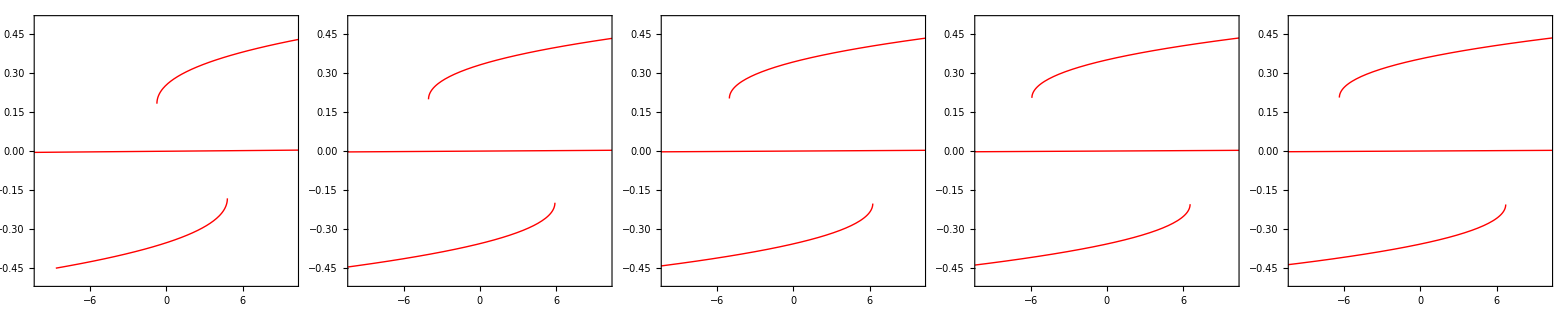

```mathematica
Tt=300;pp=1 10^-6;pmax=0.45;prop={};Elimit=10;
Plimit=0.5;LoopT500pm6=Table[Show[LGDflm["Ploop",0,Tt,pp,h->hT,λ->1,Pst->pmax](*,LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]*),PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}],{hT,{1,3,5,10,20}}];GraphicsGrid[{
LoopT500pm6},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

```mathematica
(* dynLoop1=Table[Loops["dynM",15,Tt,10^-lp,h->1,prop,col->colTab[[1+lp]],ω->wTab 10^-2,Nt->10,nst->1],{lp,0,12,2}];*)
```

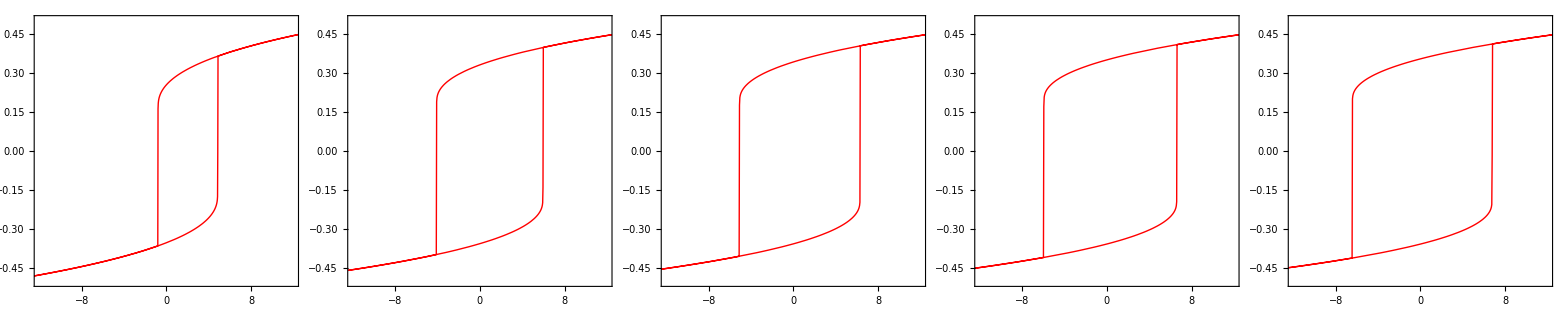

```mathematica
Tt=300;pp=1 10^-6;pmax=0.45;prop={};Elimit=12;
Plimit=0.5;LoopT500pm6=Table[Show[Loops["dynamic",hT*40,Tt,pp,h->hT,λ->1,Pst->pmax,ω->1 10^-2,Nt->10,nst->1](*,LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]*),PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}],{hT,{1,3,5,10,20}}];GraphicsGrid[{
LoopT500pm6},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

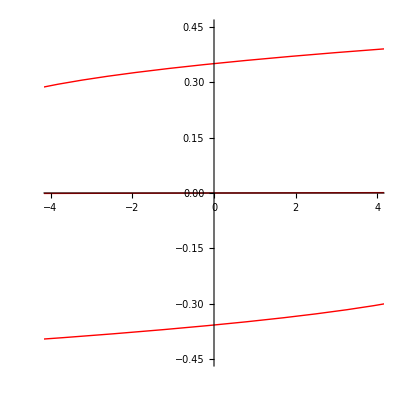

```mathematica
Elimit=4;
Plimit=0.45;Show[LGDflm["Ploop",0,Tt,pp,h->10,λ->1,Pst->0.53],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}}]
```

### static loops (planned “Figure 4”) for λ=0.2

```mathematica
(* LGDflm[slct_,U_,T_,Pe_:1,OptionsPattern[]] *)
```

```mathematica
prop={h->50,λ->0.2};
```

```mathematica
(*Tt=550;pp=1 10^-6;pmax=0.3;
Plimit=0.22;Elimit=0.2;Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Axes->True,Ticks->None,Frame->False,BaseStyle->{FontFamily->"Arial",FontSize->14}]*)
```

```mathematica
(*Tt=400;pp=0;pmax=0.51;Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]*)
```

```mathematica
Tt=200;pp=1 10^0;pmax=0.59;
Plimit=0.595;LoopT200pe0=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=200;pp=1 10^-4;pmax=0.58;
Plimit=0.595;LoopT200pm4=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=200;pp=1 10^-6;pmax=0.55;
Plimit=0.595;LoopT200pm6=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-3.85,3.85},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=300;pp=1 10^4;pmax=0.59;
Plimit=0.595;Elimit=0.99;LoopT300pe4=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=300;pp=1 10^0;pmax=0.59;
Plimit=0.595;LoopT300pe0=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=300;pp=1 10^-4;pmax=0.58;
Plimit=0.595;LoopT300pm4=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=300;pp=1 10^-6;pmax=0.55;
Plimit=0.595;LoopT300pm6=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-3.85,3.85},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=400;pp=1 10^4;pmax=0.49;
Plimit=0.49;Elimit=0.99;LoopT400pe4=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=400;pp=1 10^0;pmax=0.59;Plimit=0.56;
LoopT400pe0=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=400;pp=1 10^-4;pmax=0.5;
Plimit=0.495;LoopT400pm4=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=400;pp=1 10^-6;pmax=0.45;
Plimit=0.42;LoopT400pm6=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-3.85,3.85},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=500;pp=1 10^4;pmax=0.325;
Plimit=0.305;Elimit=0.20;LoopT500pe4=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=500;pp=1 10^0;pmax=0.45;
Plimit=0.425;LoopT500pe0=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=500;pp=1 10^-4;pmax=0.33;
Plimit=0.305;LoopT500pm4=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=500;pp=1 10^-6;pmax=0.32;
Plimit=0.305;LoopT500pm6=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
GraphicsGrid[{
{LoopT300pe4,LoopT400pe4,LoopT500pe4},
{LoopT300pe0,LoopT400pe0,LoopT500pe0},
{LoopT300pm4,LoopT400pm4,LoopT500pm4},
{LoopT300pm6,LoopT400pm6,LoopT500pm6}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

### static loops (planned “Figure 4”) for λ=2

```mathematica
(* LGDflm[slct_,U_,T_,Pe_:1,OptionsPattern[]] *)
```

```mathematica
prop={h->50,λ->2};
```

```mathematica
Plimit=0.587;Elimit=1.05;
```

```mathematica
LGDflm["LGDtst",0,Tt,pp,prop,Pst->pmax]
```

```mathematica
Tt=200;pp=1 10^4;pmax=0.65;
LoopLmb2T200pe4=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=200;pp=1 10^0;pmax=0.64;
LoopLmb2T200pe0=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=200;pp=1 10^-4;pmax=0.65;
LoopLmb2T200pm4=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=200;pp=1 10^-6;
LoopLmb2T200pm6=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Plimit=0.587;Elimit=1.95;
```

```mathematica
Tt=300;pp=1 10^4;pmax=0.63;
LoopLmb2T300pe4=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=300;pp=1 10^0;pmax=0.65;
LoopLmb2T300pe0=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=300;pp=1 10^-4;pmax=0.65;
LoopLmb2T300pm4=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=300;pp=1 10^-6;pmax=0.55;
LoopLmb2T300pm6=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-5.85,5.85},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Plimit=0.587;Elimit=3.8;
```

```mathematica
Tt=400;pp=1 10^4;pmax=0.49;
LoopLmb2T400pe4=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=400;pp=1 10^0;pmax=0.66;
LoopLmb2T400pe0=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-1.95,1.95},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=400;pp=1 10^-4;pmax=0.5;
LoopLmb2T400pm4=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=400;pp=1 10^-6;pmax=0.45;
LoopLmb2T400pm6=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-5.85,5.85},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Plimit=0.595;Elimit=0.99;
```

```mathematica
Tt=500;pp=1 10^4;pmax=0.325;
LoopLmb2T500pe4=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},PlotRange->{{-0.405,0.405},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=500;pp=1 10^0;pmax=0.65;
LoopLmb2T500pe0=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-0.2,0.2},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=500;pp=1 10^-4;pmax=0.33;
LoopLmb2T500pm4=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-0.405,0.405},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=500;pp=1 10^-6;pmax=0.32;
LoopLmb2T500pm6=Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
GraphicsGrid[{
{LoopLmb2T200pe4,LoopLmb2T300pe4,LoopLmb2T400pe4,LoopLmb2T500pe4},(**)
{LoopLmb2T200pe0,LoopLmb2T300pe0,LoopLmb2T400pe0,LoopLmb2T500pe0},
{LoopLmb2T200pm4,LoopLmb2T300pm4,LoopLmb2T400pm4,LoopLmb2T500pm4},
{LoopLmb2T200pm6,LoopLmb2T300pm6,LoopLmb2T400pm6,LoopLmb2T500pm6}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

## Phase diagrams

### Phase diagram: zero and non-zero field cases

```mathematica
Show[Graphics[{}],PlotRange->{{190,610},{-6.1,0.15}},Frame->True,FrameStyle->Directive[Black,Thick],FrameTicks->{Automatic,Flatten[Table[If[m≠1,{n+Log[10,m],""},{n,If[True(*EvenQ[n]*),Superscript[10,n],""]}],{n,-6,6},{m,1,10}],1],Automatic,Flatten[Table[If[m≠1,{n+Log[10,m],""},{n,""}],{n,-6,6},{m,1,10}],1]},BaseStyle->{FontFamily->"Arial",FontSize->16},AspectRatio->1/1.5]
```

```mathematica
(* LGDflm[slct_,U_,T_,Pe_:1,OptionsPattern[]] *)
```

```mathematica
prop={Ef->0,h->5,λ->2};PhaseDiagZeroEh5=ContourPlot[LGDflm["Nph",0,Tt,10^lpe,prop],{Tt,300,600},{lpe,-6,0},Contours->{0,1,2,3},PlotRange->All,FrameStyle->Directive[Black,Thick],PlotPoints->200,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->16},ColorFunctionScaling->False,ColorFunction->(PhaseColors[#]&),AspectRatio->1/1.5(*(ColorData["Rainbow"][(#/6)]&)*)]
```

```mathematica
prop={h->5,λ->2};PhaseDiagh5=ContourPlot[LGDflm["Nph",0,Tt,10^lpe,prop],{Tt,300,600},{lpe,-6,0},Contours->{0,1,2,3},PlotRange->All,FrameStyle->Directive[Black,Thick],PlotPoints->200,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12},ColorFunctionScaling->False,ColorFunction->(PhaseColors[#]&),ContourShading->None]
```

```mathematica
Show[PhaseDiagZeroEh5,(*PhaseDiagh5,*)PlotRange->{{298,602},{-6.1,0.1}},FrameTicks->{Automatic,Flatten[Table[If[m≠1,{n+Log[10,m],""},{n,If[True(*EvenQ[n]*),Superscript[10,n],""]}],{n,-6,6},{m,1,10}],1],Automatic,Flatten[Table[If[m≠1,{n+Log[10,m],""},{n,""}],{n,-6,6},{m,1,10}],1]},BaseStyle->{FontFamily->"Arial",FontSize->16},AspectRatio->1/1.5]
```

```mathematica
prop={Ef->0,h->50,λ->2};PhaseDiagZeroE=ContourPlot[LGDflm["Nph",0,Tt,10^lpe,prop],{Tt,300,600},{lpe,-6,6},Contours->{0,1,2,3},PlotRange->All,FrameStyle->Directive[Black,Thick],PlotPoints->100,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->16},ColorFunctionScaling->False,ColorFunction->(PhaseColors[#]&),AspectRatio->1/1.5(*(ColorData["Rainbow"][(#/6)]&)*)]
```

```mathematica
prop={h->50,λ->2};PhaseDiag=ContourPlot[LGDflm["Nph",0,Tt,10^lpe,prop],{Tt,300,600},{lpe,-6,6},Contours->{0,1,2,3},PlotRange->All,FrameStyle->Directive[Black,Thick],PlotPoints->200,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12},ColorFunctionScaling->False,ColorFunction->(PhaseColors[#]&),ContourShading->None]
```

```mathematica
Show[PhaseDiagZeroE,PhaseDiag,PlotRange->{{298,602},{-6.1,6.1}},FrameTicks->{Automatic,Flatten[Table[If[m≠1,{n+Log[10,m],""},{n,If[EvenQ[n],Superscript[10,n],""]}],{n,-6,6},{m,1,10}],1],Automatic,Table[{n,""},{n,-6,6,2}]},BaseStyle->{FontFamily->"Arial",FontSize->16},AspectRatio->1/1.5]
```

```mathematica
Show[PhaseDiagZeroE,PlotRange->{{298,602},{-6.1,0.05}},FrameTicks->{Automatic,Flatten[Table[If[m≠1,{n+Log[10,m],""},{n,If[True,Superscript[10,n],""]}],{n,-6,6},{m,1,10}],1],Automatic,Table[{n,""},{n,-6,6,1}]},BaseStyle->{FontFamily->"Arial",FontSize->16},AspectRatio->1/1.5]
```

```mathematica
prop={h->50,λ->0.2};PhaseDiag=ContourPlot[LGDflm["Nph",0,Tt,10^lpe,prop],{Tt,300,600},{lpe,-6,6},Contours->{0,1,2,3},PlotRange->All,FrameStyle->Directive[Black,Thick],PlotPoints->200,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12},ColorFunctionScaling->False,ColorFunction->(PhaseColors[#]&),ContourShading->None]
```

```mathematica
prop={h->50,λ->0.2};ZeroAlphaP=ContourPlot[(LGDflm["LGDtst",0,Tt,10^lpe,prop][[1]])==0,{Tt,300,600},{lpe,-6,6},Contours->1,PlotRange->All,FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[{Thick,Dotted,Black}],BaseStyle->{FontFamily->"Arial",FontSize->12},ContourShading->None]
```

```mathematica
Show[PhaseDiagZeroE,ZeroAlphaP(*,PhaseDiag*),PlotRange->{{298,602},{-6.1,6.1}},FrameTicks->{Automatic,Flatten[Table[If[m≠1,{n+Log[10,m],""},{n,If[EvenQ[n],Superscript[10,n],""]}],{n,-6,6},{m,1,10}],1],Automatic,Table[{n,""},{n,-6,6,2}]},BaseStyle->{FontFamily->"Arial",FontSize->16},AspectRatio->1/1.5]
```

### Pext=0. (planned "Figure 2")

#### Phase diagram

```mathematica
PhaseDiagU0pe0=ContourPlot[LGDflm["Nph",0,Tt,0,prop],{Tt,190,610},{lpe,-1,1},Contours->{0,1,2,3},PlotRange->All,AspectRatio->2/3,Frame->None,PlotPoints->{200,2},ContourLines->False,ColorFunctionScaling->False,ColorFunction->(PhaseColors[#]&)(*(ColorData["Rainbow"][(#/6)]&)*)]
```

```mathematica
Show[PhaseDiagU0pe0,Frame->{{False,False},{True,False}},FrameStyle->Directive[Medium,Black],BaseStyle->{FontFamily->"Arial",FontSize->8}]
```

#### dynamic loops

```mathematica
(* LGDflm[slct_,U_,T_,Pe_:1,OptionsPattern[]]*)
```

```mathematica
prop={h->50,λ->0.2,Ae->10^3,τA->1 10^-2};pex=0;
```

```mathematica
wTab={0.3,3,10,30,100};colTab={Black,Red,Magenta,Blue,Darker[Green],Purple,Brown};
```

```mathematica
(* loop development with frequency at T=500 *)
```

```mathematica
PdynT500tab=Table[LGDflm["dynamic",10,500,pex,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}];
Show[PdynT500tab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24},Epilog->Inset[Framed[Style["T=500 K",24],Background->ParaPale],{0.22,-0.48},{Right,Bottom}],PlotRange->All,ImageSize->350]
```

```mathematica
(* loop development with frequency at T=480 *)
```

```mathematica
(*PdynT480tab=Table[LGDflm["dynamic",15,480,pex,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}];
Show[PdynT480tab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24},Epilog->Inset[Framed[Style["T=480 K",24],Background->FerroBlue],{1.07,-0.31},{Right,Bottom}],PlotRange->All]*)
```

```mathematica
(* loop development with frequency at T=450 *)
```

```mathematica
PdynT450tab=Table[LGDflm["dynamic",12.5,450,pex,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->10,nst->1],{i,1,Length[wTab]}];
Show[PdynT450tab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24},Epilog->Inset[Framed[Style["T=450 K",24],Background->FerroBlue],{0.27,-0.50},{Right,Bottom}],PlotRange->All,ImageSize->350]
```

```mathematica
PdynT200tab=Table[LGDflm["dynamic",100,200,pex,prop,col->colTab[[i]],ω->wTab[[i]] 10^-2,Nt->20,nst->1],{i,1,Length[wTab]}];
Show[PdynT200tab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24},Epilog->Inset[Framed[Style["T=200 K",24],Background->FerroBlue],{2.1,-0.79},{Right,Bottom}],PlotRange->{-0.75,0.75},ImageSize->350]
```

```mathematica
PdynT450tab=Table[LGDflm["dynamic",16,450,pex,prop,col->If[aa==0,Red,Blue],ω->0.05 10^-2,Nt->10,nst->1,Ae->aa],{aa,{0.,10^-10}}];
Show[PdynT450tab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24},Epilog->Inset[Framed[Style["T=450 K",24],Background->FerroBlue],{1.07,-0.31},{Right,Bottom}],PlotRange->All]
```

```mathematica
(* Scan of Subscript[U, max] for T=200 K *)
```

```mathematica
PdynTstTab=Table[LGDflm["dynamic",Uu,200,0,prop,col->Red,ω->1 10^-2,Nt->9,Ae->1 10^-5],{Uu,{1,3,10,30,95}}];
Show[PdynTstTab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24}(*,Epilog->Inset[Framed[Style["T=300 K",24],Background->FerroBlue],{5.3,-0.42},{Right,Bottom}]*),PlotRange->All]
```

```mathematica
PdynT200tab=Table[LGDflm["dynamic",Uu,200,0,prop,col->RGBColor[Uu/7.0,0,1-Uu/7],ω->2 10^-2,Nt->8],{Uu,{1,2,3,4,5,7}}];
Show[PdynT200tab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24},Epilog->Inset[Framed[Style["T=200 K",24],Background->FerroBlue],{5.3,-0.42},{Right,Bottom}],PlotRange->{{-5,5},{-0.39,0.39}}]
```

```mathematica
PdynT450tab=Table[LGDflm["dynamic",Uu,450,0,prop,col->RGBColor[Uu/5.0,0,1-Uu/5],ω->0.1 10^-2,Nt->10,Ae->0 10^-59],{Uu,{1,2,5.0,10,15}}];
```

```mathematica
Show[PdynT450tab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24},Epilog->Inset[Framed[Style["T=450 K",24],Background->FerroBlue],{1.07,-0.31},{Right,Bottom}],PlotRange->All]
```

```mathematica
PdynT480tab=Table[LGDflm["dynamic",Uu,480,0,prop,col->RGBColor[Uu/2,0,1-Uu/2],ω->0.1 10^-2,Nt->5],{Uu,{0.25,0.5,1,2}}];
```

```mathematica
Show[PdynT480tab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24},Epilog->Inset[Framed[Style["T=480 K",24],Background->FerroBlue],{1.07,-0.31},{Right,Bottom}],PlotRange->{{-1,1},{-0.29,0.29}}]
```

```mathematica
PdynT500tab=Table[LGDflm["dynamic",Uu,500,0,prop,col->RGBColor[Uu/2.0,0,1-Uu^2/2],ω->0.03 10^-2,Nt->30],{Uu,{0.25,0.5,1,2}}];
```

```mathematica
Show[PdynT500tab,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->24},Epilog->Inset[Framed[Style["T=500 K",24],Background->ParaPale],{1.05,-0.31},{Right,Bottom}],PlotRange->All]
```

#### Free energy contous

```mathematica
(*EnergyT250pe0=Show[EnergyT250pe0,Epilog->Inset[Framed[Style["T=250 K",20],Background->LightGreen],{0.5,0.42},{Right,Bottom}]]*)
```

```mathematica
uu=0;
```

```mathematica
prop={h->50,λ->0.2};
```

```mathematica
Tt=480;EnergyT480pe0=ContourPlot[10^3 LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.4,0.4},{aa,-0.35,0.35},Contours->Table[n,{n,-23/10,23/10,1/10}],PlotRange->{-2.4,2.4},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[Automatic,LegendMargins->10,LabelStyle->{Black,FontSize->20}],{{1,0.5},{0,0.5}}]]
```

```mathematica
Show[EnergyT480pe0,Epilog->Inset[Framed[Style["T=480 K",20],Background->White],{0.405,0.27},{Right,Bottom}]]
```

```mathematica
10^3 LGDflm["Fmin",uu,Tt,0,Pst->0,Ast->0.21,prop]
```

```mathematica
Tt=450;EnergyT450pe0=ContourPlot[10^3 LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.49,0.49},{aa,-0.42,0.42},Contours->Table[n,{n,-72/10,72/10,3/10}],PlotRange->{-7.5,7.5},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[Automatic,LegendMargins->10,LabelStyle->{Black,FontSize->20}],{{1,0.5},{0,0.5}}]]
```

```mathematica
Show[EnergyT450pe0,Epilog->Inset[Framed[Style["T=450 K",20],Background->White],{0.5,0.29},{Right,Bottom}]]
```

```mathematica
Tt=200;EnergyT200pe0=ContourPlot[10^3 LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.7,0.7},{aa,-0.6,0.6},Contours->80,PlotRange->{-79,79},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->20},ContourStyle->Directive[Thin,Black],ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-80,80}},LegendMargins->10,LabelStyle->{Black,FontSize->20}],{{1,0.5},{0,0.5}}],Epilog->Inset[Framed[Style["T=200 K",20],Background->White],{0.71,0.47},{Right,Bottom}]]
```

```mathematica
Tt=250;EnergyT250pe0=ContourPlot[LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.55,0.55},Contours->100,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray],ColorFunction->(ColorData["TemperatureMap"][#^2]&),Epilog->Inset[Framed[Style["T=250 K",12],Background->LightGreen],{0.5,0.42},{Right,Bottom}]](*LakeColors*)
```

```mathematica
Tt=300;EnergyT300pe0=ContourPlot[LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.55,0.55},Contours->120,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12},ColorFunction->(ColorData["TemperatureMap"][#^2]&),Epilog->Inset[Framed[Style["T=300 K",12],Background->LightGreen],{0.5,0.42},{Right,Bottom}]]
```

```mathematica
Tt=350;EnergyT350pe0=ContourPlot[LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.55,0.55},Contours->100,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12},ColorFunction->(ColorData["TemperatureMap"][#^2]&),Epilog->Inset[Framed[Style["T=350 K",12],Background->LightGreen],{0.5,0.42},{Right,Bottom}]]
```

```mathematica
Tt=400;EnergyT400pe0=ContourPlot[LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.55,0.55},Contours->100,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->100,ContourLines->False,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12},ColorFunction->(ColorData["TemperatureMap"][#^2]&),Epilog->Inset[Framed[Style["T=400 K",24],Background->FerroBlue],{0.51,0.41},{Right,Bottom}]]
```

```mathematica
Tt=450;EnergyT450pe0=ContourPlot[LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.55,0.55},Contours->100,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->100,ContourLines->False,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->24},ColorFunction->(ColorData["TemperatureMap"][#^2]&),Epilog->Inset[Framed[Style["T=450 K",24],Background->FerroBlue],{0.51,0.41},{Right,Bottom}]]
```

```mathematica
Tt=490;EnergyT500pe0=ContourPlot[LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.55,0.55},Contours->100,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->100,ContourLines->False,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12},ColorFunction->(ColorData["TemperatureMap"][#^2]&),Epilog->Inset[Framed[Style["T=490 K",12],Background->LightGreen],{0.5,0.42},{Right,Bottom}]]
```

```mathematica
10^5 LGDflm["func",uu,Tt,0,Pst->0,Ast->0.21,prop]
```

```mathematica
Tt=500;EnergyT500pe0=ContourPlot[10^3 LGDflm["func",uu,Tt,0,Pst->pp,Ast->aa,prop],{pp,-0.35,0.35},{aa,-0.32,0.32},Contours->Table[i,{i,0,1,0.05}],PlotRange->{-0.02,1.02},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->20},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{0,1}},LegendMargins->10,LabelStyle->{Black,FontSize->20}],{{1,0.5},{0,0.5}}]]
```

```mathematica
Show[EnergyT500pe0,Epilog->Inset[Framed[Style["T=500 K",20],Background->White],{0.35,0.25},{Right,Bottom}]]
```

```mathematica
GraphicsGrid[{{EnergyT250pe0,EnergyT300pe0,EnergyT350pe0},{EnergyT400pe0,EnergyT450pe0,EnergyT500pe0}},Spacings->{Scaled[0.00],Scaled[0.0]}]
```

#### static loops

```mathematica
prop={h->50,λ->0.2};pp=0;
```

```mathematica
Tt=550;pmax=0.3;
Plimit=0.22;Elimit=0.2;Show[LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Axes->True,Ticks->None,Frame->False,BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=200;pmax=0.65;
Plimit=0.6;Elimit=1.45;LoopT200p0=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->18},ImageSize->300,Epilog->Inset[Framed[Style["T=200 K",18],Background->FerroBlue],{1.49,-0.64},{Right,Bottom}],PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}}]
```

```mathematica
Show[LoopT200p0,Frame->True,FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->False,BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=450;pmax=0.59;
Plimit=0.57;Elimit=0.73;LoopT450p0=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->18},ImageSize->300,Epilog->Inset[Framed[Style["T=450 K",18],Background->FerroBlue],{0.785,-0.615},{Right,Bottom}]]
```

```mathematica
Tt=480;pmax=0.59;
Plimit=0.595;Elimit=0.2;LoopT480p0=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->14}]
```

```mathematica
Tt=500;pmax=0.59;
Plimit=0.39;Elimit=0.1;LoopT500p0=Show[{LGDflm["Ploop",0,Tt,pp,prop,Pst->pmax],LGDflm["Aloop",0,Tt,pp,prop,Pst->pmax,col->Blue]},PlotRange->{{-Elimit,Elimit},{-Plimit,Plimit}},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Arial",FontSize->18},ImageSize->300,Epilog->Inset[Framed[Style["T=500 K",18],Background->ParaPale],{0.107,-0.42},{Right,Bottom}]]
```

### Free energy contours at different P_ext

#### Figure 3 at λ=0.2

```mathematica
prop={h->50,λ->0.2};
```

```mathematica
uu=0;
```

```mathematica
ContourPlot[10^3 LGDflm["func",uu,300,10^0,Pst->pp,Ast->aa,prop],{pp,-0.62,0.62},{aa,-0.55,0.55},Contours->100,PlotRange->{-46,46},Frame->False,PlotPoints->20,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&)]
```

```mathematica
10^3 LGDflm["Fmin",uu,300,10^-6,prop]
```

```mathematica
ContourPlot[10^3 LGDflm["func",uu,300,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.51,0.51},{aa,-0.57,0.57},Contours->30,PlotRange->{-45.33,45.33},Frame->False,PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&)]
```

```mathematica
10^3 LGDflm["Fmin",uu,550,10^-6,prop]
```

```mathematica
ContourPlot[10^3 LGDflm["func",uu,550,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.1,0.1},{aa,-0.1,0.1},Contours->30,PlotRange->{-1,1},Frame->False,PlotPoints->20,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunctionScaling->True,ColorFunction->(ColorData["Rainbow"][#+1/2]&)]
```

```mathematica
(* T=300 K *)
```

```mathematica
EnergyT300dG02pe4=ContourPlot[10^3 LGDflm["func",uu,300,10^4,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.55,0.55},Contours->100,PlotRange->{-46,46},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-45,45}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
EnergyT300dG02pe0=ContourPlot[10^3 LGDflm["func",uu,300,10^0,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.55,0.55},Contours->100,PlotRange->{-46,46},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-45,45}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
EnergyT300dG02pm4=ContourPlot[10^3 LGDflm["func",uu,300,10^-4,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.55,0.55},Contours->100,PlotRange->{-46,46},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-45,45}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
EnergyT300dG02pm6=ContourPlot[10^3 LGDflm["func",uu,300,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.55,0.55},Contours->30,PlotRange->{-46,46},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-45,45}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
10^3 LGDflm["Fmin",uu,300,10^-6,prop]
```

```mathematica
(* T=400 K *)
```

```mathematica
EnergyT400dG02pe4=ContourPlot[10^3 LGDflm["func",uu,400,10^4,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.5,0.5},Contours->20,PlotRange->{-18,18},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-18,18}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
EnergyT400dG02pe0=ContourPlot[10^3 LGDflm["func",uu,400,10^0,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.5,0.5},Contours->20,PlotRange->{-18,18},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-18,18}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
EnergyT400dG02pm4=ContourPlot[10^3 LGDflm["func",uu,400,10^-4,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.5,0.5},Contours->20,PlotRange->{-18,18},FrameStyle->Directive[Black,Thick],PlotPoints->10,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-18,18}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
(*10^3 LGDflm["Fmin",uu,400,10^-4,prop]*)
```

```mathematica
EnergyT400dG02pm6=ContourPlot[10^3 LGDflm["func",uu,400,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.5,0.5},Contours->12,PlotRange->{-26,26},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-26,26}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
(* T=500 K *)
```

```mathematica
10^3 LGDflm["Fmin",uu,500,10^4,prop]
```

```mathematica
EnergyT500dG02pe4=ContourPlot[10^3 LGDflm["func",uu,500,10^4,Pst->pp,Ast->aa,prop],{pp,-0.11,0.31},{aa,-0.26,0.26},Contours->Table[i,{i,-0.5,0.5,0.05}],PlotRange->{-0.5,0.5},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-0.5,0.5}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
EnergyT500dG02pe0=ContourPlot[10^3 LGDflm["func",uu,500,10^0,Pst->pp,Ast->aa,prop],{pp,-0.31,0.31},{aa,-0.31,0.31},Contours->Table[i,{i,0,0.5,0.05}],PlotRange->{0,0.5},FrameStyle->Directive[Black,Thick],PlotPoints->10,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#+1/2]&),PlotLegends->Placed[BarLegend[{ColorData["Rainbow"][#+1/2]&,{0,0.5}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
10^3 LGDflm["Fmin",uu,500,10^-4,prop]
```

```mathematica
EnergyT500dG02pm4=ContourPlot[10^3 LGDflm["func",uu,500,10^-4,Pst->pp,Ast->aa,prop],{pp,-0.31,0.11},{aa,-0.26,0.26},Contours->Table[i,{i,-0.5,0.5,0.05}],PlotRange->{-0.5,0.5},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-0.5,0.5}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
10^3 LGDflm["Fmin",uu,500,10^-6,prop]
```

```mathematica
EnergyT500dG02pm6=ContourPlot[10^3 LGDflm["func",uu,500,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.31,0.31},{aa,-0.31,0.31},Contours->11,PlotRange->{-2,2},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-2,2}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
GraphicsGrid[{
{EnergyT300dG02pe4,EnergyT400dG02pe4,EnergyT500dG02pe4},
{EnergyT300dG02pe0,EnergyT400dG02pe0,EnergyT500dG02pe0},
{EnergyT300dG02pm4,EnergyT400dG02pm4,EnergyT500dG02pm4},
{EnergyT300dG02pm6,EnergyT400dG02pm6,EnergyT500dG02pm6}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

#### Figure 3 at λ=2

```mathematica
prop={h->50,λ->2};
```

```mathematica
uu=0;
```

```mathematica
10^3 LGDflm["Fmin",uu,300,10^0,prop]
```

```mathematica
(*ContourPlot[10^3 LGDflm["func",uu,300,10^0,Pst->pp,Ast->aa,prop],{pp,-0.62,0.62},{aa,-0.55,0.55},Contours->100,PlotRange->{-46,46},Frame->False,PlotPoints->20,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&)]*)
```

```mathematica
ContourPlot[10^3 LGDflm["func",uu,300,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.51,0.51},{aa,-0.57,0.57},Contours->30,PlotRange->{-45.33,45.33},Frame->False,PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&)]
```

```mathematica
10^3 LGDflm["Fmin",uu,200,10^0,prop]
```

```mathematica
Fmin=-79;EnergyT200lmb2pe4=ContourPlot[10^3 LGDflm["func",uu,200,10^4,Pst->pp,Ast->aa,prop],{pp,-0.63,0.63},{aa,-0.61,0.61},Contours->30,PlotRange->{Fmin,-Fmin},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{Fmin,-Fmin}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
Fmin=-79;EnergyT200lmb2pe0=ContourPlot[10^3 LGDflm["func",uu,200,10^0,Pst->pp,Ast->aa,prop],{pp,-0.63,0.63},{aa,-0.61,0.61},Contours->30,PlotRange->{Fmin,-Fmin},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{Fmin,-Fmin}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
Fmin=-79;EnergyT200lmb2pm4=ContourPlot[10^3 LGDflm["func",uu,200,10^-4,Pst->pp,Ast->aa,prop],{pp,-0.63,0.63},{aa,-0.61,0.61},Contours->30,PlotRange->{Fmin,-Fmin},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{Fmin,-Fmin}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
10^3 LGDflm["Fmin",uu,200,10^-6,prop]
```

```mathematica
Fmin=-79;EnergyT200lmb2pm6=ContourPlot[10^3 LGDflm["func",uu,200,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.63,0.63},{aa,-0.61,0.61},Contours->30,PlotRange->{Fmin,-Fmin},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{Fmin,-Fmin}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
(* T=300 K *)
```

```mathematica
EnergyT300lmb2pe4=ContourPlot[10^3 LGDflm["func",uu,300,10^4,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.55,0.55},Contours->30,PlotRange->{-46,46},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-45,45}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
EnergyT300lmb2pe0=ContourPlot[10^3 LGDflm["func",uu,300,10^0,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.55,0.55},Contours->30,PlotRange->{-46,46},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-45,45}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
EnergyT300lmb2pm4=ContourPlot[10^3 LGDflm["func",uu,300,10^-4,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.55,0.55},Contours->30,PlotRange->{-46,46},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-45,45}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
Fmin=-116;EnergyT300lmb2pm6=ContourPlot[10^3 LGDflm["func",uu,300,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.55,0.55},Contours->30,PlotRange->{Fmin,-Fmin},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{Fmin,-Fmin}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
10^3 LGDflm["Fmin",uu,300,10^-6,prop]
```

```mathematica
(* T=400 K *)
```

```mathematica
EnergyT400lmb2pe4=ContourPlot[10^3 LGDflm["func",uu,400,10^4,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.5,0.5},Contours->20,PlotRange->{-19,19},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-19,19}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
EnergyT400lmb2pe0=ContourPlot[10^3 LGDflm["func",uu,400,10^0,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.5,0.5},Contours->20,PlotRange->{-18,18},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-18,18}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
EnergyT400lmb2pm4=ContourPlot[10^3 LGDflm["func",uu,400,10^-4,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.5,0.5},Contours->20,PlotRange->{-19,19},FrameStyle->Directive[Black,Thick],PlotPoints->10,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-19,19}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]];
```

```mathematica
10^3 LGDflm["Fmin",uu,400,10^-4,prop](**)
```

```mathematica
EnergyT400lmb2pm6=ContourPlot[10^3 LGDflm["func",uu,400,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.55,0.55},{aa,-0.6,0.6},Contours->12,PlotRange->{-260,260},FrameStyle->Directive[Black,Thick],PlotPoints->10,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-26,26}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
(* T=500 K *)
```

```mathematica
10^3 LGDflm["Fmin",uu,400,10^-6,prop]
```

```mathematica
EnergyT500lmb2pe4=ContourPlot[10^3 LGDflm["func",uu,500,10^4,Pst->pp,Ast->aa,prop],{pp,-0.11,0.31},{aa,-0.33,0.33},Contours->Table[i,{i,-4.5,4.5,0.5}],PlotRange->{-4.5,4.5},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-4.5,4.5}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
EnergyT500lmb2pe0=ContourPlot[10^3 LGDflm["func",uu,500,10^0,Pst->pp,Ast->aa,prop],{pp,-0.11,0.11},{aa,-0.31,0.31},Contours->Table[i,{i,0,1,0.05}],PlotRange->{0,1},FrameStyle->Directive[Black,Thick],PlotPoints->10,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/2+1/2]&),PlotLegends->Placed[BarLegend[{ColorData["Rainbow"][#/2+1/2]&,{0,1}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
10^3 LGDflm["Fmin",uu,500,10^-4,prop]
```

```mathematica
EnergyT500lmb2pm4=ContourPlot[10^3 LGDflm["func",uu,500,10^-4,Pst->pp,Ast->aa,prop],{pp,-0.31,0.11},{aa,-0.33,0.33},Contours->Table[i,{i,-4.5,4.5,0.5}],PlotRange->{-4.5,4.5},FrameStyle->Directive[Black,Thick],PlotPoints->30,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-4.5,4.5}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
10^3 LGDflm["Fmin",uu,500,10^-6,prop]
```

```mathematica
EnergyT500lmb2pm6=ContourPlot[10^3 LGDflm["func",uu,500,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.31,0.31},{aa,-0.41,0.41},Contours->11,PlotRange->{-18,18},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,ContourStyle->Directive[Thin,Black],BaseStyle->{FontFamily->"Arial",FontSize->14},ColorFunction->(ColorData["Rainbow"][#]&),PlotLegends->Placed[BarLegend[{"Rainbow",{-2,2}},LegendMargins->0,LabelStyle->{Black,FontSize->10}],{{1,0.5},{0,0.5}}]]
```

```mathematica
GraphicsGrid[{
{EnergyT200lmb2pe4,EnergyT300lmb2pe4,EnergyT400lmb2pe4,EnergyT500lmb2pe4},
{EnergyT200lmb2pe0,EnergyT300lmb2pe0,EnergyT400lmb2pe0,EnergyT500lmb2pe0},
{EnergyT200lmb2pm4,EnergyT300lmb2pm4,EnergyT400lmb2pm4,EnergyT500lmb2pm4},
{EnergyT200lmb2pm6,EnergyT300lmb2pm6,EnergyT400lmb2pm6,EnergyT500lmb2pm6}},Spacings->{Scaled[0.01],Scaled[0.0]}]
```

#### δG_1=0.2

```mathematica
EnergyT300dG02pe6=ContourPlot[LGDflm["func",uu,Tt,10^6,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12}];
```

```mathematica
EnergyT300dG02pe4=ContourPlot[LGDflm["func",uu,Tt,10^4,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT300dG02pe3=ContourPlot[LGDflm["func",uu,Tt,10^3,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT300dG02pe2=ContourPlot[LGDflm["func",uu,Tt,10^2,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT300dG02pe0=ContourPlot[LGDflm["func",uu,Tt,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT250dG02pe0=ContourPlot[LGDflm["func",uu,250,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT350dG02pe0=ContourPlot[LGDflm["func",uu,350,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT400dG02pe0=ContourPlot[LGDflm["func",uu,400,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT450dG02pe0=ContourPlot[LGDflm["func",uu,450,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT500dG02pe0=ContourPlot[LGDflm["func",uu,500,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT550dG02pe0=ContourPlot[LGDflm["func",uu,550,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT600dG02pe0=ContourPlot[LGDflm["func",uu,600,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->100,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT450dG02pe0
```

```mathematica
GraphicsGrid[{{EnergyT300dG02pe0,EnergyT300dG02pe2,EnergyT300dG02pe4,EnergyT300dG02pe8},{EnergyT300dG02pe0,EnergyT350dG02pe0,EnergyT400dG02pe0,EnergyT450dG02pe0}},Spacings->{Scaled[0.00],Scaled[0.0]}]
```

```mathematica
Plot[LGDflm["func",uu,499.5,1,Pst->-10^-6,Ast->pp,prop],{pp,-0.25,0.25},PlotRange->All,FrameStyle->Directive[Black,Thick],PlotPoints->50,BaseStyle->{FontFamily->"Arial",FontSize->12}]
```

#### δG_1=0.2

```mathematica
prop={dG1->0.2,h->50,λ->0.2};
```

```mathematica
uu=0;Tt=300;
```

```mathematica
EnergyT300pe6=ContourPlot[LGDflm["func",uu,Tt,10^6,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12}]
```

```mathematica
EnergyT300pe5=ContourPlot[LGDflm["func",uu,Tt,10^5,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
EnergyT300pe0=ContourPlot[LGDflm["func",uu,Tt,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
EnergyT300pm5=ContourPlot[LGDflm["func",uu,Tt,10^-5,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,(*ColorFunction->"LakeColors",*)ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
EnergyT300pm6=ContourPlot[LGDflm["func",uu,Tt,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,(*ColorFunction->"LakeColors",*)ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
EnergyT300pm8=ContourPlot[LGDflm["func",uu,Tt,10^-8,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,(*ColorFunction->"LakeColors",*)ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
GraphicsGrid[{{EnergyT300pe0,EnergyT300pe5,EnergyT300pe6},{EnergyT300pm5,EnergyT300pm6,EnergyT300pm8}},Spacings->{Scaled[0.00],Scaled[0.0]}]
```

#### δG_1=0.1

```mathematica
prop={dG1->0.1,h->50,λ->0.2};
```

```mathematica
uu=0;Tt=300;
```

```mathematica
EnergyT300dG01pe6=ContourPlot[LGDflm["func",uu,Tt,10^6,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,ContourStyle->Directive[Thin,Gray],BaseStyle->{FontFamily->"Arial",FontSize->12}]
```

```mathematica
EnergyT300dG01pe5=ContourPlot[LGDflm["func",uu,Tt,10^5,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
EnergyT300dG01pe4=ContourPlot[LGDflm["func",uu,Tt,10^4,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT300dG01pe3=ContourPlot[LGDflm["func",uu,Tt,10^3,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT300dG01pe2=ContourPlot[LGDflm["func",uu,Tt,10^2,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT300dG01pe0=ContourPlot[LGDflm["func",uu,Tt,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
EnergyT300dG01pm5=ContourPlot[LGDflm["func",uu,Tt,10^-5,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,(*ColorFunction->"LakeColors",*)ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
EnergyT300dG01pm6=ContourPlot[LGDflm["func",uu,Tt,10^-6,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,(*ColorFunction->"LakeColors",*)ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
EnergyT300dG01pm8=ContourPlot[LGDflm["func",uu,Tt,10^-8,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,(*ColorFunction->"LakeColors",*)ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]]
```

```mathematica
EnergyT250dG01pe0=ContourPlot[LGDflm["func",uu,250,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT350dG01pe0=ContourPlot[LGDflm["func",uu,350,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT400dG01pe0=ContourPlot[LGDflm["func",uu,400,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT500dG01pe0=ContourPlot[LGDflm["func",uu,500,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
EnergyT600dG01pe0=ContourPlot[LGDflm["func",uu,600,1,Pst->pp,Ast->aa,prop],{pp,-0.5,0.5},{aa,-0.5,0.5},Contours->50,PlotRange->{Automatic,0},FrameStyle->Directive[Black,Thick],PlotPoints->50,ContourLines->True,BaseStyle->{FontFamily->"Arial",FontSize->12},ContourStyle->Directive[Thin,Gray]];
```

```mathematica
GraphicsGrid[{{EnergyT300dG01pe0,EnergyT300dG01pe2,EnergyT300dG01pe3,EnergyT300dG01pe4},{EnergyT250dG01pe0,EnergyT300dG01pe0,EnergyT350dG01pe0,EnergyT400dG01pe0}},Spacings->{Scaled[0.00],Scaled[0.0]}]
```

```mathematica
GraphicsGrid[{{EnergyT300dG01pe0,EnergyT300dG01pe2,EnergyT300dG01pe3,EnergyT300dG01pe4},{EnergyT300dG01pe0,EnergyT400dG01pe0,EnergyT500dG01pe0,EnergyT600dG01pe0}},Spacings->{Scaled[0.00],Scaled[0.0]}]
```